```mathematica
For[j=2,j<=100,j++,
If[PrimeQ[j]||(IntegerQ[Sqrt[j]]&&PrimeQ[Sqrt[j]]),
Print["n = ",j," and diff = ",Floor[Sqrt[4j/3]]-Floor[Sqrt[j]]//N]];
];
```

n = 2 and diff = 0.

n = 3 and diff = 1.

n = 4 and diff = 0.

n = 5 and diff = 0.

n = 7 and diff = 1.

n = 9 and diff = 0.

n = 11 and diff = 0.

n = 13 and diff = 1.

n = 17 and diff = 0.

n = 19 and diff = 1.

n = 23 and diff = 1.

n = 25 and diff = 0.

n = 29 and diff = 1.

n = 31 and diff = 1.

n = 37 and diff = 1.

n = 41 and diff = 1.

n = 43 and diff = 1.

n = 47 and diff = 1.

n = 49 and diff = 1.

n = 53 and diff = 1.

n = 59 and diff = 1.

n = 61 and diff = 2.

n = 67 and diff = 1.

n = 71 and diff = 1.

n = 73 and diff = 1.

n = 79 and diff = 2.

n = 83 and diff = 1.

n = 89 and diff = 1.

n = 97 and diff = 2.

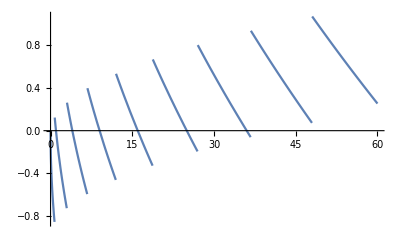

```mathematica
Plot[Floor[Sqrt[4i/3]]-Sqrt[i],{i,0,60}]
```

```mathematica
For[j=3,j<=1000,j++,
i=j;
Print["i = ",i," and diff = ",Floor[Sqrt[4i/3]]-Sqrt[i]//N];
];
```

i = 3 and diff = 0.267949

i = 4 and diff = 0.

i = 5 and diff = -0.236068

i = 6 and diff = -0.44949

i = 7 and diff = 0.354249

i = 8 and diff = 0.171573

i = 9 and diff = 0.

i = 10 and diff = -0.162278

i = 11 and diff = -0.316625

i = 12 and diff = 0.535898

i = 13 and diff = 0.394449

i = 14 and diff = 0.258343

i = 15 and diff = 0.127017

i = 16 and diff = 0.

i = 17 and diff = -0.123106

i = 18 and diff = -0.242641

i = 19 and diff = 0.641101

i = 20 and diff = 0.527864

i = 21 and diff = 0.417424

i = 22 and diff = 0.309584

i = 23 and diff = 0.204168

i = 24 and diff = 0.101021

i = 25 and diff = 0.

i = 26 and diff = -0.0990195

i = 27 and diff = 0.803848

i = 28 and diff = 0.708497

i = 29 and diff = 0.614835

i = 30 and diff = 0.522774

i = 31 and diff = 0.432236

i = 32 and diff = 0.343146

i = 33 and diff = 0.255437

i = 34 and diff = 0.169048

i = 35 and diff = 0.0839202

i = 36 and diff = 0.

i = 37 and diff = 0.917237

i = 38 and diff = 0.835586

i = 39 and diff = 0.755002

i = 40 and diff = 0.675445

i = 41 and diff = 0.596876

i = 42 and diff = 0.519259

i = 43 and diff = 0.442561

i = 44 and diff = 0.36675

i = 45 and diff = 0.291796

i = 46 and diff = 0.21767

i = 47 and diff = 0.144345

i = 48 and diff = 1.0718

i = 49 and diff = 1.

i = 50 and diff = 0.928932

i = 51 and diff = 0.858572

i = 52 and diff = 0.788897

i = 53 and diff = 0.71989

i = 54 and diff = 0.651531

i = 55 and diff = 0.583802

i = 56 and diff = 0.516685

i = 57 and diff = 0.450166

i = 58 and diff = 0.384227

i = 59 and diff = 0.318854

i = 60 and diff = 0.254033

i = 61 and diff = 1.18975

i = 62 and diff = 1.12599

i = 63 and diff = 1.06275

i = 64 and diff = 1.

i = 65 and diff = 0.937742

i = 66 and diff = 0.875962

i = 67 and diff = 0.814647

i = 68 and diff = 0.753789

i = 69 and diff = 0.693376

i = 70 and diff = 0.6334

i = 71 and diff = 0.57385

i = 72 and diff = 0.514719

i = 73 and diff = 0.455996

i = 74 and diff = 0.397675

i = 75 and diff = 1.33975

i = 76 and diff = 1.2822

i = 77 and diff = 1.22504

i = 78 and diff = 1.16824

i = 79 and diff = 1.11181

i = 80 and diff = 1.05573

i = 81 and diff = 1.

i = 82 and diff = 0.944615

i = 83 and diff = 0.889566

i = 84 and diff = 0.834849

i = 85 and diff = 0.780456

i = 86 and diff = 0.726382

i = 87 and diff = 0.672621

i = 88 and diff = 0.619168

i = 89 and diff = 0.566019

i = 90 and diff = 0.513167

i = 91 and diff = 1.46061

i = 92 and diff = 1.40834

i = 93 and diff = 1.35635

i = 94 and diff = 1.30464

i = 95 and diff = 1.25321

i = 96 and diff = 1.20204

i = 97 and diff = 1.15114

i = 98 and diff = 1.10051

i = 99 and diff = 1.05013

i = 100 and diff = 1.

i = 101 and diff = 0.950124

i = 102 and diff = 0.900495

i = 103 and diff = 0.851108

i = 104 and diff = 0.801961

i = 105 and diff = 0.753049

i = 106 and diff = 0.70437

i = 107 and diff = 0.65592

i = 108 and diff = 1.6077

i = 109 and diff = 1.55969

i = 110 and diff = 1.51191

i = 111 and diff = 1.46435

i = 112 and diff = 1.41699

i = 113 and diff = 1.36985

i = 114 and diff = 1.32292

i = 115 and diff = 1.27619

i = 116 and diff = 1.22967

i = 117 and diff = 1.18335

i = 118 and diff = 1.13722

i = 119 and diff = 1.09129

i = 120 and diff = 1.04555

i = 121 and diff = 1.

i = 122 and diff = 0.954639

i = 123 and diff = 0.909463

i = 124 and diff = 0.864471

i = 125 and diff = 0.81966

i = 126 and diff = 0.775028

i = 127 and diff = 1.73057

i = 128 and diff = 1.68629

i = 129 and diff = 1.64218

i = 130 and diff = 1.59825

i = 131 and diff = 1.55448

i = 132 and diff = 1.51087

i = 133 and diff = 1.46744

i = 134 and diff = 1.42416

i = 135 and diff = 1.38105

i = 136 and diff = 1.3381

i = 137 and diff = 1.2953

i = 138 and diff = 1.25266

i = 139 and diff = 1.21017

i = 140 and diff = 1.16784

i = 141 and diff = 1.12566

i = 142 and diff = 1.08362

i = 143 and diff = 1.04174

i = 144 and diff = 1.

i = 145 and diff = 0.958405

i = 146 and diff = 0.916954

i = 147 and diff = 1.87564

i = 148 and diff = 1.83447

i = 149 and diff = 1.79344

i = 150 and diff = 1.75255

i = 151 and diff = 1.71179

i = 152 and diff = 1.67117

i = 153 and diff = 1.63068

i = 154 and diff = 1.59033

i = 155 and diff = 1.5501

i = 156 and diff = 1.51

i = 157 and diff = 1.47004

i = 158 and diff = 1.43019

i = 159 and diff = 1.39048

i = 160 and diff = 1.35089

i = 161 and diff = 1.31142

i = 162 and diff = 1.27208

i = 163 and diff = 1.23285

i = 164 and diff = 1.19375

i = 165 and diff = 1.15477

i = 166 and diff = 1.1159

i = 167 and diff = 1.07715

i = 168 and diff = 1.03852

i = 169 and diff = 2.

i = 170 and diff = 1.9616

i = 171 and diff = 1.9233

i = 172 and diff = 1.88512

i = 173 and diff = 1.84705

i = 174 and diff = 1.80909

i = 175 and diff = 1.77124

i = 176 and diff = 1.7335

i = 177 and diff = 1.69587

i = 178 and diff = 1.65834

i = 179 and diff = 1.62091

i = 180 and diff = 1.58359

i = 181 and diff = 1.54638

i = 182 and diff = 1.50926

i = 183 and diff = 1.47225

i = 184 and diff = 1.43534

i = 185 and diff = 1.39853

i = 186 and diff = 1.36182

i = 187 and diff = 1.32521

i = 188 and diff = 1.28869

i = 189 and diff = 1.25227

i = 190 and diff = 1.21595

i = 191 and diff = 1.17973

i = 192 and diff = 2.14359

i = 193 and diff = 2.10756

i = 194 and diff = 2.07161

i = 195 and diff = 2.03576

i = 196 and diff = 2.

i = 197 and diff = 1.96433

i = 198 and diff = 1.92875

i = 199 and diff = 1.89326

i = 200 and diff = 1.85786

i = 201 and diff = 1.82255

i = 202 and diff = 1.78733

i = 203 and diff = 1.75219

i = 204 and diff = 1.71714

i = 205 and diff = 1.68218

i = 206 and diff = 1.6473

i = 207 and diff = 1.61251

i = 208 and diff = 1.57779

i = 209 and diff = 1.54317

i = 210 and diff = 1.50862

i = 211 and diff = 1.47416

i = 212 and diff = 1.43978

i = 213 and diff = 1.40548

i = 214 and diff = 1.37126

i = 215 and diff = 1.33712

i = 216 and diff = 1.30306

i = 217 and diff = 2.26908

i = 218 and diff = 2.23518

i = 219 and diff = 2.20135

i = 220 and diff = 2.1676

i = 221 and diff = 2.13393

i = 222 and diff = 2.10034

i = 223 and diff = 2.06682

i = 224 and diff = 2.03337

i = 225 and diff = 2.

i = 226 and diff = 1.9667

i = 227 and diff = 1.93348

i = 228 and diff = 1.90033

i = 229 and diff = 1.86725

i = 230 and diff = 1.83425

i = 231 and diff = 1.80132

i = 232 and diff = 1.76845

i = 233 and diff = 1.73566

i = 234 and diff = 1.70294

i = 235 and diff = 1.67029

i = 236 and diff = 1.63771

i = 237 and diff = 1.6052

i = 238 and diff = 1.57275

i = 239 and diff = 1.54038

i = 240 and diff = 1.50807

i = 241 and diff = 1.47583

i = 242 and diff = 1.44365

i = 243 and diff = 2.41154

i = 244 and diff = 2.3795

i = 245 and diff = 2.34752

i = 246 and diff = 2.31561

i = 247 and diff = 2.28377

i = 248 and diff = 2.25198

i = 249 and diff = 2.22027

i = 250 and diff = 2.18861

i = 251 and diff = 2.15702

i = 252 and diff = 2.12549

i = 253 and diff = 2.09403

i = 254 and diff = 2.06262

i = 255 and diff = 2.03128

i = 256 and diff = 2.

i = 257 and diff = 1.96878

i = 258 and diff = 1.93762

i = 259 and diff = 1.90652

i = 260 and diff = 1.87548

i = 261 and diff = 1.84451

i = 262 and diff = 1.81359

i = 263 and diff = 1.78273

i = 264 and diff = 1.75192

i = 265 and diff = 1.72118

i = 266 and diff = 1.69049

i = 267 and diff = 1.65987

i = 268 and diff = 1.62929

i = 269 and diff = 1.59878

i = 270 and diff = 1.56832

i = 271 and diff = 2.53792

i = 272 and diff = 2.50758

i = 273 and diff = 2.47729

i = 274 and diff = 2.44705

i = 275 and diff = 2.41688

i = 276 and diff = 2.38675

i = 277 and diff = 2.35668

i = 278 and diff = 2.32667

i = 279 and diff = 2.29671

i = 280 and diff = 2.2668

i = 281 and diff = 2.23695

i = 282 and diff = 2.20714

i = 283 and diff = 2.1774

i = 284 and diff = 2.1477

i = 285 and diff = 2.11806

i = 286 and diff = 2.08847

i = 287 and diff = 2.05893

i = 288 and diff = 2.02944

i = 289 and diff = 2.

i = 290 and diff = 1.97061

i = 291 and diff = 1.94128

i = 292 and diff = 1.91199

i = 293 and diff = 1.88276

i = 294 and diff = 1.85357

i = 295 and diff = 1.82444

i = 296 and diff = 1.79535

i = 297 and diff = 1.76631

i = 298 and diff = 1.73732

i = 299 and diff = 1.70838

i = 300 and diff = 2.67949

i = 301 and diff = 2.65065

i = 302 and diff = 2.62185

i = 303 and diff = 2.5931

i = 304 and diff = 2.5644

i = 305 and diff = 2.53575

i = 306 and diff = 2.50714

i = 307 and diff = 2.47858

i = 308 and diff = 2.45007

i = 309 and diff = 2.4216

i = 310 and diff = 2.39318

i = 311 and diff = 2.36481

i = 312 and diff = 2.33648

i = 313 and diff = 2.30819

i = 314 and diff = 2.27995

i = 315 and diff = 2.25176

i = 316 and diff = 2.22361

i = 317 and diff = 2.19551

i = 318 and diff = 2.16745

i = 319 and diff = 2.13943

i = 320 and diff = 2.11146

i = 321 and diff = 2.08353

i = 322 and diff = 2.05564

i = 323 and diff = 2.0278

i = 324 and diff = 2.

i = 325 and diff = 1.97224

i = 326 and diff = 1.94453

i = 327 and diff = 1.91686

i = 328 and diff = 1.88923

i = 329 and diff = 1.86164

i = 330 and diff = 1.8341

i = 331 and diff = 2.80659

i = 332 and diff = 2.77913

i = 333 and diff = 2.75171

i = 334 and diff = 2.72433

i = 335 and diff = 2.69699

i = 336 and diff = 2.6697

i = 337 and diff = 2.64244

i = 338 and diff = 2.61522

i = 339 and diff = 2.58805

i = 340 and diff = 2.56091

i = 341 and diff = 2.53381

i = 342 and diff = 2.50676

i = 343 and diff = 2.47974

i = 344 and diff = 2.45276

i = 345 and diff = 2.42582

i = 346 and diff = 2.39892

i = 347 and diff = 2.37206

i = 348 and diff = 2.34524

i = 349 and diff = 2.31846

i = 350 and diff = 2.29171

i = 351 and diff = 2.26501

i = 352 and diff = 2.23834

i = 353 and diff = 2.21171

i = 354 and diff = 2.18511

i = 355 and diff = 2.15856

i = 356 and diff = 2.13204

i = 357 and diff = 2.10556

i = 358 and diff = 2.07911

i = 359 and diff = 2.0527

i = 360 and diff = 2.02633

i = 361 and diff = 2.

i = 362 and diff = 1.9737

i = 363 and diff = 2.94744

i = 364 and diff = 2.92122

i = 365 and diff = 2.89503

i = 366 and diff = 2.86887

i = 367 and diff = 2.84276

i = 368 and diff = 2.81667

i = 369 and diff = 2.79063

i = 370 and diff = 2.76462

i = 371 and diff = 2.73864

i = 372 and diff = 2.7127

i = 373 and diff = 2.68679

i = 374 and diff = 2.66092

i = 375 and diff = 2.63508

i = 376 and diff = 2.60928

i = 377 and diff = 2.58351

i = 378 and diff = 2.55778

i = 379 and diff = 2.53208

i = 380 and diff = 2.50641

i = 381 and diff = 2.48078

i = 382 and diff = 2.45518

i = 383 and diff = 2.42961

i = 384 and diff = 2.40408

i = 385 and diff = 2.37858

i = 386 and diff = 2.35312

i = 387 and diff = 2.32768

i = 388 and diff = 2.30228

i = 389 and diff = 2.27692

i = 390 and diff = 2.25158

i = 391 and diff = 2.22628

i = 392 and diff = 2.20101

i = 393 and diff = 2.17577

i = 394 and diff = 2.15057

i = 395 and diff = 2.12539

i = 396 and diff = 2.10025

i = 397 and diff = 3.07514

i = 398 and diff = 3.05006

i = 399 and diff = 3.02502

i = 400 and diff = 3.

i = 401 and diff = 2.97502

i = 402 and diff = 2.95006

i = 403 and diff = 2.92514

i = 404 and diff = 2.90025

i = 405 and diff = 2.87539

i = 406 and diff = 2.85056

i = 407 and diff = 2.82576

i = 408 and diff = 2.80099

i = 409 and diff = 2.77625

i = 410 and diff = 2.75154

i = 411 and diff = 2.72687

i = 412 and diff = 2.70222

i = 413 and diff = 2.6776

i = 414 and diff = 2.65301

i = 415 and diff = 2.62845

i = 416 and diff = 2.60392

i = 417 and diff = 2.57942

i = 418 and diff = 2.55495

i = 419 and diff = 2.53051

i = 420 and diff = 2.5061

i = 421 and diff = 2.48172

i = 422 and diff = 2.45736

i = 423 and diff = 2.43304

i = 424 and diff = 2.40874

i = 425 and diff = 2.38447

i = 426 and diff = 2.36023

i = 427 and diff = 2.33602

i = 428 and diff = 2.31184

i = 429 and diff = 2.28768

i = 430 and diff = 2.26356

i = 431 and diff = 2.23946

i = 432 and diff = 3.21539

i = 433 and diff = 3.19135

i = 434 and diff = 3.16733

i = 435 and diff = 3.14335

i = 436 and diff = 3.11939

i = 437 and diff = 3.09546

i = 438 and diff = 3.07155

i = 439 and diff = 3.04767

i = 440 and diff = 3.02382

i = 441 and diff = 3.

i = 442 and diff = 2.9762

i = 443 and diff = 2.95243

i = 444 and diff = 2.92869

i = 445 and diff = 2.90498

i = 446 and diff = 2.88129

i = 447 and diff = 2.85763

i = 448 and diff = 2.83399

i = 449 and diff = 2.81038

i = 450 and diff = 2.7868

i = 451 and diff = 2.76324

i = 452 and diff = 2.73971

i = 453 and diff = 2.7162

i = 454 and diff = 2.69272

i = 455 and diff = 2.66927

i = 456 and diff = 2.64584

i = 457 and diff = 2.62244

i = 458 and diff = 2.59907

i = 459 and diff = 2.57571

i = 460 and diff = 2.55239

i = 461 and diff = 2.52909

i = 462 and diff = 2.50581

i = 463 and diff = 2.48257

i = 464 and diff = 2.45934

i = 465 and diff = 2.43614

i = 466 and diff = 2.41297

i = 467 and diff = 2.38982

i = 468 and diff = 2.36669

i = 469 and diff = 3.34359

i = 470 and diff = 3.32052

i = 471 and diff = 3.29747

i = 472 and diff = 3.27444

i = 473 and diff = 3.25144

i = 474 and diff = 3.22846

i = 475 and diff = 3.20551

i = 476 and diff = 3.18258

i = 477 and diff = 3.15967

i = 478 and diff = 3.13679

i = 479 and diff = 3.11393

i = 480 and diff = 3.0911

i = 481 and diff = 3.06829

i = 482 and diff = 3.0455

i = 483 and diff = 3.02274

i = 484 and diff = 3.

i = 485 and diff = 2.97728

i = 486 and diff = 2.95459

i = 487 and diff = 2.93192

i = 488 and diff = 2.90928

i = 489 and diff = 2.88666

i = 490 and diff = 2.86406

i = 491 and diff = 2.84148

i = 492 and diff = 2.81893

i = 493 and diff = 2.7964

i = 494 and diff = 2.77389

i = 495 and diff = 2.7514

i = 496 and diff = 2.72894

i = 497 and diff = 2.7065

i = 498 and diff = 2.68409

i = 499 and diff = 2.66169

i = 500 and diff = 2.63932

i = 501 and diff = 2.61697

i = 502 and diff = 2.59464

i = 503 and diff = 2.57234

i = 504 and diff = 2.55006

i = 505 and diff = 2.52779

i = 506 and diff = 2.50556

i = 507 and diff = 3.48334

i = 508 and diff = 3.46114

i = 509 and diff = 3.43897

i = 510 and diff = 3.41682

i = 511 and diff = 3.39469

i = 512 and diff = 3.37258

i = 513 and diff = 3.3505

i = 514 and diff = 3.32843

i = 515 and diff = 3.30639

i = 516 and diff = 3.28437

i = 517 and diff = 3.26237

i = 518 and diff = 3.24039

i = 519 and diff = 3.21843

i = 520 and diff = 3.19649

i = 521 and diff = 3.17458

i = 522 and diff = 3.15268

i = 523 and diff = 3.13081

i = 524 and diff = 3.10895

i = 525 and diff = 3.08712

i = 526 and diff = 3.06531

i = 527 and diff = 3.04352

i = 528 and diff = 3.02175

i = 529 and diff = 3.

i = 530 and diff = 2.97827

i = 531 and diff = 2.95656

i = 532 and diff = 2.93487

i = 533 and diff = 2.91321

i = 534 and diff = 2.89156

i = 535 and diff = 2.86993

i = 536 and diff = 2.84833

i = 537 and diff = 2.82674

i = 538 and diff = 2.80517

i = 539 and diff = 2.78363

i = 540 and diff = 2.7621

i = 541 and diff = 2.74059

i = 542 and diff = 2.71911

i = 543 and diff = 2.69764

i = 544 and diff = 2.67619

i = 545 and diff = 2.65476

i = 546 and diff = 2.63336

i = 547 and diff = 3.61197

i = 548 and diff = 3.5906

i = 549 and diff = 3.56925

i = 550 and diff = 3.54792

i = 551 and diff = 3.52661

i = 552 and diff = 3.50532

i = 553 and diff = 3.48405

i = 554 and diff = 3.4628

i = 555 and diff = 3.44156

i = 556 and diff = 3.42035

i = 557 and diff = 3.39915

i = 558 and diff = 3.37798

i = 559 and diff = 3.35682

i = 560 and diff = 3.33568

i = 561 and diff = 3.31456

i = 562 and diff = 3.29346

i = 563 and diff = 3.27238

i = 564 and diff = 3.25132

i = 565 and diff = 3.23027

i = 566 and diff = 3.20925

i = 567 and diff = 3.18824

i = 568 and diff = 3.16725

i = 569 and diff = 3.14628

i = 570 and diff = 3.12533

i = 571 and diff = 3.10439

i = 572 and diff = 3.08348

i = 573 and diff = 3.06258

i = 574 and diff = 3.0417

i = 575 and diff = 3.02084

i = 576 and diff = 3.

i = 577 and diff = 2.97918

i = 578 and diff = 2.95837

i = 579 and diff = 2.93758

i = 580 and diff = 2.91681

i = 581 and diff = 2.89606

i = 582 and diff = 2.87532

i = 583 and diff = 2.85461

i = 584 and diff = 2.83391

i = 585 and diff = 2.81323

i = 586 and diff = 2.79256

i = 587 and diff = 2.77192

i = 588 and diff = 3.75129

i = 589 and diff = 3.73068

i = 590 and diff = 3.71008

i = 591 and diff = 3.68951

i = 592 and diff = 3.66895

i = 593 and diff = 3.64841

i = 594 and diff = 3.62788

i = 595 and diff = 3.60738

i = 596 and diff = 3.58689

i = 597 and diff = 3.56642

i = 598 and diff = 3.54596

i = 599 and diff = 3.52552

i = 600 and diff = 3.5051

i = 601 and diff = 3.4847

i = 602 and diff = 3.46431

i = 603 and diff = 3.44394

i = 604 and diff = 3.42359

i = 605 and diff = 3.40325

i = 606 and diff = 3.38293

i = 607 and diff = 3.36263

i = 608 and diff = 3.34234

i = 609 and diff = 3.32207

i = 610 and diff = 3.30182

i = 611 and diff = 3.28159

i = 612 and diff = 3.26137

i = 613 and diff = 3.24116

i = 614 and diff = 3.22098

i = 615 and diff = 3.20081

i = 616 and diff = 3.18065

i = 617 and diff = 3.16052

i = 618 and diff = 3.14039

i = 619 and diff = 3.12029

i = 620 and diff = 3.1002

i = 621 and diff = 3.08013

i = 622 and diff = 3.06007

i = 623 and diff = 3.04003

i = 624 and diff = 3.02001

i = 625 and diff = 3.

i = 626 and diff = 2.98001

i = 627 and diff = 2.96003

i = 628 and diff = 2.94007

i = 629 and diff = 2.92013

i = 630 and diff = 2.9002

i = 631 and diff = 3.88029

i = 632 and diff = 3.86039

i = 633 and diff = 3.84051

i = 634 and diff = 3.82064

i = 635 and diff = 3.80079

i = 636 and diff = 3.78096

i = 637 and diff = 3.76114

i = 638 and diff = 3.74134

i = 639 and diff = 3.72155

i = 640 and diff = 3.70178

i = 641 and diff = 3.68202

i = 642 and diff = 3.66228

i = 643 and diff = 3.64256

i = 644 and diff = 3.62284

i = 645 and diff = 3.60315

i = 646 and diff = 3.58347

i = 647 and diff = 3.56381

i = 648 and diff = 3.54416

i = 649 and diff = 3.52452

i = 650 and diff = 3.5049

i = 651 and diff = 3.4853

i = 652 and diff = 3.46571

i = 653 and diff = 3.44614

i = 654 and diff = 3.42658

i = 655 and diff = 3.40703

i = 656 and diff = 3.3875

i = 657 and diff = 3.36799

i = 658 and diff = 3.34849

i = 659 and diff = 3.329

i = 660 and diff = 3.30953

i = 661 and diff = 3.29008

i = 662 and diff = 3.27064

i = 663 and diff = 3.25121

i = 664 and diff = 3.2318

i = 665 and diff = 3.21241

i = 666 and diff = 3.19302

i = 667 and diff = 3.17366

i = 668 and diff = 3.1543

i = 669 and diff = 3.13497

i = 670 and diff = 3.11564

i = 671 and diff = 3.09633

i = 672 and diff = 3.07704

i = 673 and diff = 3.05776

i = 674 and diff = 3.03849

i = 675 and diff = 4.01924

i = 676 and diff = 4.

i = 677 and diff = 3.98078

i = 678 and diff = 3.96157

i = 679 and diff = 3.94237

i = 680 and diff = 3.92319

i = 681 and diff = 3.90402

i = 682 and diff = 3.88487

i = 683 and diff = 3.86573

i = 684 and diff = 3.84661

i = 685 and diff = 3.8275

i = 686 and diff = 3.8084

i = 687 and diff = 3.78932

i = 688 and diff = 3.77025

i = 689 and diff = 3.75119

i = 690 and diff = 3.73215

i = 691 and diff = 3.71312

i = 692 and diff = 3.69411

i = 693 and diff = 3.67511

i = 694 and diff = 3.65612

i = 695 and diff = 3.63715

i = 696 and diff = 3.61819

i = 697 and diff = 3.59924

i = 698 and diff = 3.58031

i = 699 and diff = 3.56139

i = 700 and diff = 3.54249

i = 701 and diff = 3.5236

i = 702 and diff = 3.50472

i = 703 and diff = 3.48585

i = 704 and diff = 3.467

i = 705 and diff = 3.44816

i = 706 and diff = 3.42934

i = 707 and diff = 3.41053

i = 708 and diff = 3.39173

i = 709 and diff = 3.37295

i = 710 and diff = 3.35417

i = 711 and diff = 3.33542

i = 712 and diff = 3.31667

i = 713 and diff = 3.29794

i = 714 and diff = 3.27922

i = 715 and diff = 3.26052

i = 716 and diff = 3.24182

i = 717 and diff = 3.22314

i = 718 and diff = 3.20448

i = 719 and diff = 3.18582

i = 720 and diff = 3.16718

i = 721 and diff = 4.14856

i = 722 and diff = 4.12994

i = 723 and diff = 4.11134

i = 724 and diff = 4.09275

i = 725 and diff = 4.07418

i = 726 and diff = 4.05561

i = 727 and diff = 4.03706

i = 728 and diff = 4.01852

i = 729 and diff = 4.

i = 730 and diff = 3.98149

i = 731 and diff = 3.96299

i = 732 and diff = 3.9445

i = 733 and diff = 3.92603

i = 734 and diff = 3.90757

i = 735 and diff = 3.88912

i = 736 and diff = 3.87068

i = 737 and diff = 3.85226

i = 738 and diff = 3.83384

i = 739 and diff = 3.81545

i = 740 and diff = 3.79706

i = 741 and diff = 3.77868

i = 742 and diff = 3.76032

i = 743 and diff = 3.74197

i = 744 and diff = 3.72364

i = 745 and diff = 3.70531

i = 746 and diff = 3.687

i = 747 and diff = 3.6687

i = 748 and diff = 3.65041

i = 749 and diff = 3.63214

i = 750 and diff = 3.61387

i = 751 and diff = 3.59562

i = 752 and diff = 3.57738

i = 753 and diff = 3.55915

i = 754 and diff = 3.54094

i = 755 and diff = 3.52274

i = 756 and diff = 3.50455

i = 757 and diff = 3.48637

i = 758 and diff = 3.4682

i = 759 and diff = 3.45005

i = 760 and diff = 3.4319

i = 761 and diff = 3.41377

i = 762 and diff = 3.39565

i = 763 and diff = 3.37755

i = 764 and diff = 3.35945

i = 765 and diff = 3.34137

i = 766 and diff = 3.32329

i = 767 and diff = 3.30524

i = 768 and diff = 4.28719

i = 769 and diff = 4.26915

i = 770 and diff = 4.25113

i = 771 and diff = 4.23311

i = 772 and diff = 4.21511

i = 773 and diff = 4.19712

i = 774 and diff = 4.17914

i = 775 and diff = 4.16118

i = 776 and diff = 4.14322

i = 777 and diff = 4.12528

i = 778 and diff = 4.10735

i = 779 and diff = 4.08943

i = 780 and diff = 4.07152

i = 781 and diff = 4.05362

i = 782 and diff = 4.03574

i = 783 and diff = 4.01786

i = 784 and diff = 4.

i = 785 and diff = 3.98215

i = 786 and diff = 3.96431

i = 787 and diff = 3.94648

i = 788 and diff = 3.92866

i = 789 and diff = 3.91086

i = 790 and diff = 3.89306

i = 791 and diff = 3.87528

i = 792 and diff = 3.85751

i = 793 and diff = 3.83974

i = 794 and diff = 3.82199

i = 795 and diff = 3.80426

i = 796 and diff = 3.78653

i = 797 and diff = 3.76881

i = 798 and diff = 3.75111

i = 799 and diff = 3.73341

i = 800 and diff = 3.71573

i = 801 and diff = 3.69806

i = 802 and diff = 3.6804

i = 803 and diff = 3.66275

i = 804 and diff = 3.64511

i = 805 and diff = 3.62748

i = 806 and diff = 3.60986

i = 807 and diff = 3.59225

i = 808 and diff = 3.57466

i = 809 and diff = 3.55707

i = 810 and diff = 3.5395

i = 811 and diff = 3.52194

i = 812 and diff = 3.50439

i = 813 and diff = 3.48685

i = 814 and diff = 3.46931

i = 815 and diff = 3.4518

i = 816 and diff = 3.43429

i = 817 and diff = 4.41679

i = 818 and diff = 4.3993

i = 819 and diff = 4.38182

i = 820 and diff = 4.36436

i = 821 and diff = 4.3469

i = 822 and diff = 4.32946

i = 823 and diff = 4.31202

i = 824 and diff = 4.2946

i = 825 and diff = 4.27719

i = 826 and diff = 4.25978

i = 827 and diff = 4.24239

i = 828 and diff = 4.22501

i = 829 and diff = 4.20764

i = 830 and diff = 4.19028

i = 831 and diff = 4.17293

i = 832 and diff = 4.15559

i = 833 and diff = 4.13826

i = 834 and diff = 4.12094

i = 835 and diff = 4.10363

i = 836 and diff = 4.08634

i = 837 and diff = 4.06905

i = 838 and diff = 4.05177

i = 839 and diff = 4.0345

i = 840 and diff = 4.01725

i = 841 and diff = 4.

i = 842 and diff = 3.98276

i = 843 and diff = 3.96554

i = 844 and diff = 3.94832

i = 845 and diff = 3.93112

i = 846 and diff = 3.91392

i = 847 and diff = 3.89674

i = 848 and diff = 3.87956

i = 849 and diff = 3.8624

i = 850 and diff = 3.84524

i = 851 and diff = 3.8281

i = 852 and diff = 3.81096

i = 853 and diff = 3.79384

i = 854 and diff = 3.77672

i = 855 and diff = 3.75962

i = 856 and diff = 3.74252

i = 857 and diff = 3.72544

i = 858 and diff = 3.70836

i = 859 and diff = 3.6913

i = 860 and diff = 3.67424

i = 861 and diff = 3.6572

i = 862 and diff = 3.64016

i = 863 and diff = 3.62314

i = 864 and diff = 3.60612

i = 865 and diff = 3.58912

i = 866 and diff = 3.57212

i = 867 and diff = 4.55514

i = 868 and diff = 4.53816

i = 869 and diff = 4.52119

i = 870 and diff = 4.50424

i = 871 and diff = 4.48729

i = 872 and diff = 4.47035

i = 873 and diff = 4.45343

i = 874 and diff = 4.43651

i = 875 and diff = 4.4196

i = 876 and diff = 4.4027

i = 877 and diff = 4.38581

i = 878 and diff = 4.36894

i = 879 and diff = 4.35207

i = 880 and diff = 4.33521

i = 881 and diff = 4.31836

i = 882 and diff = 4.30152

i = 883 and diff = 4.28468

i = 884 and diff = 4.26786

i = 885 and diff = 4.25105

i = 886 and diff = 4.23425

i = 887 and diff = 4.21745

i = 888 and diff = 4.20067

i = 889 and diff = 4.1839

i = 890 and diff = 4.16713

i = 891 and diff = 4.15038

i = 892 and diff = 4.13363

i = 893 and diff = 4.11689

i = 894 and diff = 4.10017

i = 895 and diff = 4.08345

i = 896 and diff = 4.06674

i = 897 and diff = 4.05004

i = 898 and diff = 4.03335

i = 899 and diff = 4.01667

i = 900 and diff = 4.

i = 901 and diff = 3.98334

i = 902 and diff = 3.96669

i = 903 and diff = 3.95004

i = 904 and diff = 3.93341

i = 905 and diff = 3.91678

i = 906 and diff = 3.90017

i = 907 and diff = 3.88356

i = 908 and diff = 3.86696

i = 909 and diff = 3.85037

i = 910 and diff = 3.83379

i = 911 and diff = 3.81722

i = 912 and diff = 3.80066

i = 913 and diff = 3.78411

i = 914 and diff = 3.76757

i = 915 and diff = 3.75103

i = 916 and diff = 3.73451

i = 917 and diff = 3.71799

i = 918 and diff = 3.70149

i = 919 and diff = 4.68499

i = 920 and diff = 4.6685

i = 921 and diff = 4.65202

i = 922 and diff = 4.63555

i = 923 and diff = 4.61908

i = 924 and diff = 4.60263

i = 925 and diff = 4.58619

i = 926 and diff = 4.56975

i = 927 and diff = 4.55333

i = 928 and diff = 4.53691

i = 929 and diff = 4.5205

i = 930 and diff = 4.5041

i = 931 and diff = 4.48771

i = 932 and diff = 4.47132

i = 933 and diff = 4.45495

i = 934 and diff = 4.43859

i = 935 and diff = 4.42223

i = 936 and diff = 4.40588

i = 937 and diff = 4.38954

i = 938 and diff = 4.37321

i = 939 and diff = 4.35689

i = 940 and diff = 4.34058

i = 941 and diff = 4.32428

i = 942 and diff = 4.30798

i = 943 and diff = 4.29169

i = 944 and diff = 4.27542

i = 945 and diff = 4.25915

i = 946 and diff = 4.24289

i = 947 and diff = 4.22663

i = 948 and diff = 4.21039

i = 949 and diff = 4.19416

i = 950 and diff = 4.17793

i = 951 and diff = 4.16171

i = 952 and diff = 4.1455

i = 953 and diff = 4.1293

i = 954 and diff = 4.11311

i = 955 and diff = 4.09693

i = 956 and diff = 4.08075

i = 957 and diff = 4.06458

i = 958 and diff = 4.04842

i = 959 and diff = 4.03227

i = 960 and diff = 4.01613

i = 961 and diff = 4.

i = 962 and diff = 3.98388

i = 963 and diff = 3.96776

i = 964 and diff = 3.95165

i = 965 and diff = 3.93555

i = 966 and diff = 3.91946

i = 967 and diff = 3.90338

i = 968 and diff = 3.8873

i = 969 and diff = 3.87124

i = 970 and diff = 3.85518

i = 971 and diff = 3.83913

i = 972 and diff = 4.82309

i = 973 and diff = 4.80705

i = 974 and diff = 4.79103

i = 975 and diff = 4.77501

i = 976 and diff = 4.759

i = 977 and diff = 4.743

i = 978 and diff = 4.72701

i = 979 and diff = 4.71102

i = 980 and diff = 4.69505

i = 981 and diff = 4.67908

i = 982 and diff = 4.66312

i = 983 and diff = 4.64717

i = 984 and diff = 4.63123

i = 985 and diff = 4.61529

i = 986 and diff = 4.59936

i = 987 and diff = 4.58344

i = 988 and diff = 4.56753

i = 989 and diff = 4.55163

i = 990 and diff = 4.53573

i = 991 and diff = 4.51985

i = 992 and diff = 4.50397

i = 993 and diff = 4.4881

i = 994 and diff = 4.47223

i = 995 and diff = 4.45638

i = 996 and diff = 4.44053

i = 997 and diff = 4.42469

i = 998 and diff = 4.40886

i = 999 and diff = 4.39304

i = 1000 and diff = 4.37722

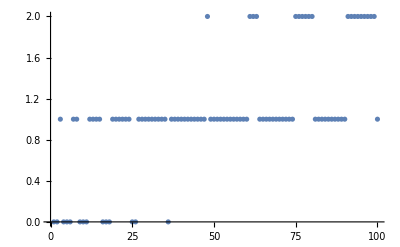

```mathematica
ListPlot[Table[Floor[Sqrt[4i/3]]-Floor[Sqrt[i]],{i,1,100}]]
```

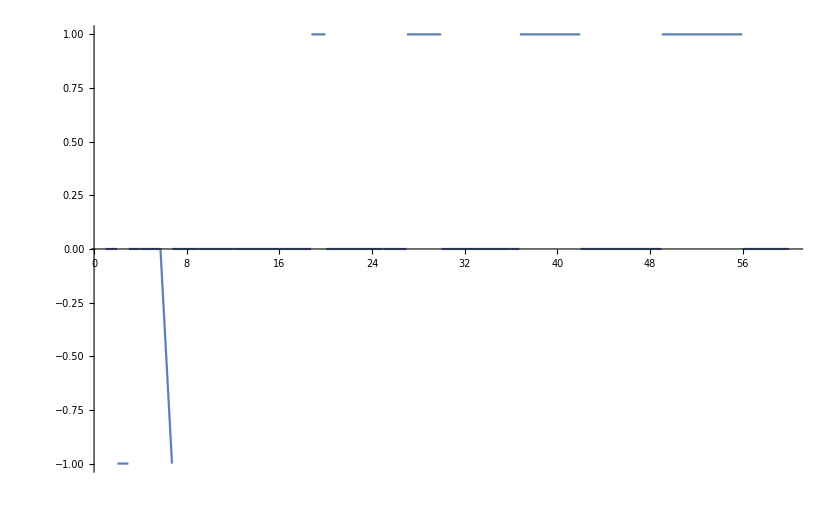

```mathematica
Plot[Floor[Sqrt[x]]-Floor[x/Floor[Sqrt[4x/3]]],{x,1,60}]
```

```mathematica
For[x=1,x<=1000,x++,
Print["x = ",x," and diff = ",Floor[Sqrt[x]]-Floor[x/Floor[Sqrt[4x/3]]]];]
```

x = 1 and diff = 0

x = 2 and diff = -1

x = 3 and diff = 0

x = 4 and diff = 0

x = 5 and diff = 0

x = 6 and diff = -1

x = 7 and diff = 0

x = 8 and diff = 0

x = 9 and diff = 0

x = 10 and diff = 0

x = 11 and diff = 0

x = 12 and diff = 0

x = 13 and diff = 0

x = 14 and diff = 0

x = 15 and diff = 0

x = 16 and diff = 0

x = 17 and diff = 0

x = 18 and diff = 0

x = 19 and diff = 1

x = 20 and diff = 0

x = 21 and diff = 0

x = 22 and diff = 0

x = 23 and diff = 0

x = 24 and diff = 0

x = 25 and diff = 0

x = 26 and diff = 0

x = 27 and diff = 1

x = 28 and diff = 1

x = 29 and diff = 1

x = 30 and diff = 0

x = 31 and diff = 0

x = 32 and diff = 0

x = 33 and diff = 0

x = 34 and diff = 0

x = 35 and diff = 0

x = 36 and diff = 0

x = 37 and diff = 1

x = 38 and diff = 1

x = 39 and diff = 1

x = 40 and diff = 1

x = 41 and diff = 1

x = 42 and diff = 0

x = 43 and diff = 0

x = 44 and diff = 0

x = 45 and diff = 0

x = 46 and diff = 0

x = 47 and diff = 0

x = 48 and diff = 0

x = 49 and diff = 1

x = 50 and diff = 1

x = 51 and diff = 1

x = 52 and diff = 1

x = 53 and diff = 1

x = 54 and diff = 1

x = 55 and diff = 1

x = 56 and diff = 0

x = 57 and diff = 0

x = 58 and diff = 0

x = 59 and diff = 0

x = 60 and diff = 0

x = 61 and diff = 1

x = 62 and diff = 1

x = 63 and diff = 0

x = 64 and diff = 1

x = 65 and diff = 1

x = 66 and diff = 1

x = 67 and diff = 1

x = 68 and diff = 1

x = 69 and diff = 1

x = 70 and diff = 1

x = 71 and diff = 1

x = 72 and diff = 0

x = 73 and diff = 0

x = 74 and diff = 0

x = 75 and diff = 1

x = 76 and diff = 1

x = 77 and diff = 1

x = 78 and diff = 1

x = 79 and diff = 1

x = 80 and diff = 0

x = 81 and diff = 1

x = 82 and diff = 1

x = 83 and diff = 1

x = 84 and diff = 1

x = 85 and diff = 1

x = 86 and diff = 1

x = 87 and diff = 1

x = 88 and diff = 1

x = 89 and diff = 1

x = 90 and diff = 0

x = 91 and diff = 1

x = 92 and diff = 1

x = 93 and diff = 1

x = 94 and diff = 1

x = 95 and diff = 1

x = 96 and diff = 1

x = 97 and diff = 1

x = 98 and diff = 1

x = 99 and diff = 0

x = 100 and diff = 1

x = 101 and diff = 1

x = 102 and diff = 1

x = 103 and diff = 1

x = 104 and diff = 1

x = 105 and diff = 1

x = 106 and diff = 1

x = 107 and diff = 1

x = 108 and diff = 1

x = 109 and diff = 1

x = 110 and diff = 1

x = 111 and diff = 1

x = 112 and diff = 1

x = 113 and diff = 1

x = 114 and diff = 1

x = 115 and diff = 1

x = 116 and diff = 1

x = 117 and diff = 1

x = 118 and diff = 1

x = 119 and diff = 1

x = 120 and diff = 0

x = 121 and diff = 1

x = 122 and diff = 1

x = 123 and diff = 1

x = 124 and diff = 1

x = 125 and diff = 1

x = 126 and diff = 1

x = 127 and diff = 2

x = 128 and diff = 2

x = 129 and diff = 2

x = 130 and diff = 1

x = 131 and diff = 1

x = 132 and diff = 1

x = 133 and diff = 1

x = 134 and diff = 1

x = 135 and diff = 1

x = 136 and diff = 1

x = 137 and diff = 1

x = 138 and diff = 1

x = 139 and diff = 1

x = 140 and diff = 1

x = 141 and diff = 1

x = 142 and diff = 1

x = 143 and diff = 0

x = 144 and diff = 1

x = 145 and diff = 1

x = 146 and diff = 1

x = 147 and diff = 2

x = 148 and diff = 2

x = 149 and diff = 2

x = 150 and diff = 2

x = 151 and diff = 2

x = 152 and diff = 2

x = 153 and diff = 2

x = 154 and diff = 1

x = 155 and diff = 1

x = 156 and diff = 1

x = 157 and diff = 1

x = 158 and diff = 1

x = 159 and diff = 1

x = 160 and diff = 1

x = 161 and diff = 1

x = 162 and diff = 1

x = 163 and diff = 1

x = 164 and diff = 1

x = 165 and diff = 1

x = 166 and diff = 1

x = 167 and diff = 1

x = 168 and diff = 0

x = 169 and diff = 2

x = 170 and diff = 2

x = 171 and diff = 2

x = 172 and diff = 2

x = 173 and diff = 2

x = 174 and diff = 2

x = 175 and diff = 2

x = 176 and diff = 2

x = 177 and diff = 2

x = 178 and diff = 2

x = 179 and diff = 2

x = 180 and diff = 1

x = 181 and diff = 1

x = 182 and diff = 1

x = 183 and diff = 1

x = 184 and diff = 1

x = 185 and diff = 1

x = 186 and diff = 1

x = 187 and diff = 1

x = 188 and diff = 1

x = 189 and diff = 1

x = 190 and diff = 1

x = 191 and diff = 1

x = 192 and diff = 1

x = 193 and diff = 1

x = 194 and diff = 1

x = 195 and diff = 1

x = 196 and diff = 2

x = 197 and diff = 2

x = 198 and diff = 2

x = 199 and diff = 2

x = 200 and diff = 2

x = 201 and diff = 2

x = 202 and diff = 2

x = 203 and diff = 2

x = 204 and diff = 2

x = 205 and diff = 2

x = 206 and diff = 2

x = 207 and diff = 2

x = 208 and diff = 1

x = 209 and diff = 1

x = 210 and diff = 1

x = 211 and diff = 1

x = 212 and diff = 1

x = 213 and diff = 1

x = 214 and diff = 1

x = 215 and diff = 1

x = 216 and diff = 1

x = 217 and diff = 2

x = 218 and diff = 2

x = 219 and diff = 2

x = 220 and diff = 2

x = 221 and diff = 1

x = 222 and diff = 1

x = 223 and diff = 1

x = 224 and diff = 1

x = 225 and diff = 2

x = 226 and diff = 2

x = 227 and diff = 2

x = 228 and diff = 2

x = 229 and diff = 2

x = 230 and diff = 2

x = 231 and diff = 2

x = 232 and diff = 2

x = 233 and diff = 2

x = 234 and diff = 2

x = 235 and diff = 2

x = 236 and diff = 2

x = 237 and diff = 2

x = 238 and diff = 1

x = 239 and diff = 1

x = 240 and diff = 1

x = 241 and diff = 1

x = 242 and diff = 1

x = 243 and diff = 2

x = 244 and diff = 2

x = 245 and diff = 2

x = 246 and diff = 2

x = 247 and diff = 2

x = 248 and diff = 2

x = 249 and diff = 2

x = 250 and diff = 2

x = 251 and diff = 2

x = 252 and diff = 1

x = 253 and diff = 1

x = 254 and diff = 1

x = 255 and diff = 1

x = 256 and diff = 2

x = 257 and diff = 2

x = 258 and diff = 2

x = 259 and diff = 2

x = 260 and diff = 2

x = 261 and diff = 2

x = 262 and diff = 2

x = 263 and diff = 2

x = 264 and diff = 2

x = 265 and diff = 2

x = 266 and diff = 2

x = 267 and diff = 2

x = 268 and diff = 2

x = 269 and diff = 2

x = 270 and diff = 1

x = 271 and diff = 2

x = 272 and diff = 2

x = 273 and diff = 2

x = 274 and diff = 2

x = 275 and diff = 2

x = 276 and diff = 2

x = 277 and diff = 2

x = 278 and diff = 2

x = 279 and diff = 2

x = 280 and diff = 2

x = 281 and diff = 2

x = 282 and diff = 2

x = 283 and diff = 2

x = 284 and diff = 2

x = 285 and diff = 1

x = 286 and diff = 1

x = 287 and diff = 1

x = 288 and diff = 1

x = 289 and diff = 2

x = 290 and diff = 2

x = 291 and diff = 2

x = 292 and diff = 2

x = 293 and diff = 2

x = 294 and diff = 2

x = 295 and diff = 2

x = 296 and diff = 2

x = 297 and diff = 2

x = 298 and diff = 2

x = 299 and diff = 2

x = 300 and diff = 2

x = 301 and diff = 2

x = 302 and diff = 2

x = 303 and diff = 2

x = 304 and diff = 2

x = 305 and diff = 2

x = 306 and diff = 2

x = 307 and diff = 2

x = 308 and diff = 2

x = 309 and diff = 2

x = 310 and diff = 2

x = 311 and diff = 2

x = 312 and diff = 2

x = 313 and diff = 2

x = 314 and diff = 2

x = 315 and diff = 2

x = 316 and diff = 2

x = 317 and diff = 2

x = 318 and diff = 2

x = 319 and diff = 2

x = 320 and diff = 1

x = 321 and diff = 1

x = 322 and diff = 1

x = 323 and diff = 1

x = 324 and diff = 2

x = 325 and diff = 2

x = 326 and diff = 2

x = 327 and diff = 2

x = 328 and diff = 2

x = 329 and diff = 2

x = 330 and diff = 2

x = 331 and diff = 3

x = 332 and diff = 3

x = 333 and diff = 3

x = 334 and diff = 3

x = 335 and diff = 3

x = 336 and diff = 2

x = 337 and diff = 2

x = 338 and diff = 2

x = 339 and diff = 2

x = 340 and diff = 2

x = 341 and diff = 2

x = 342 and diff = 2

x = 343 and diff = 2

x = 344 and diff = 2

x = 345 and diff = 2

x = 346 and diff = 2

x = 347 and diff = 2

x = 348 and diff = 2

x = 349 and diff = 2

x = 350 and diff = 2

x = 351 and diff = 2

x = 352 and diff = 2

x = 353 and diff = 2

x = 354 and diff = 2

x = 355 and diff = 2

x = 356 and diff = 2

x = 357 and diff = 1

x = 358 and diff = 1

x = 359 and diff = 1

x = 360 and diff = 1

x = 361 and diff = 2

x = 362 and diff = 2

x = 363 and diff = 3

x = 364 and diff = 3

x = 365 and diff = 3

x = 366 and diff = 3

x = 367 and diff = 3

x = 368 and diff = 3

x = 369 and diff = 3

x = 370 and diff = 3

x = 371 and diff = 3

x = 372 and diff = 3

x = 373 and diff = 3

x = 374 and diff = 2

x = 375 and diff = 2

x = 376 and diff = 2

x = 377 and diff = 2

x = 378 and diff = 2

x = 379 and diff = 2

x = 380 and diff = 2

x = 381 and diff = 2

x = 382 and diff = 2

x = 383 and diff = 2

x = 384 and diff = 2

x = 385 and diff = 2

x = 386 and diff = 2

x = 387 and diff = 2

x = 388 and diff = 2

x = 389 and diff = 2

x = 390 and diff = 2

x = 391 and diff = 2

x = 392 and diff = 2

x = 393 and diff = 2

x = 394 and diff = 2

x = 395 and diff = 2

x = 396 and diff = 1

x = 397 and diff = 2

x = 398 and diff = 2

x = 399 and diff = 2

x = 400 and diff = 3

x = 401 and diff = 3

x = 402 and diff = 3

x = 403 and diff = 3

x = 404 and diff = 3

x = 405 and diff = 3

x = 406 and diff = 3

x = 407 and diff = 3

x = 408 and diff = 3

x = 409 and diff = 3

x = 410 and diff = 3

x = 411 and diff = 3

x = 412 and diff = 3

x = 413 and diff = 3

x = 414 and diff = 2

x = 415 and diff = 2

x = 416 and diff = 2

x = 417 and diff = 2

x = 418 and diff = 2

x = 419 and diff = 2

x = 420 and diff = 2

x = 421 and diff = 2

x = 422 and diff = 2

x = 423 and diff = 2

x = 424 and diff = 2

x = 425 and diff = 2

x = 426 and diff = 2

x = 427 and diff = 2

x = 428 and diff = 2

x = 429 and diff = 2

x = 430 and diff = 2

x = 431 and diff = 2

x = 432 and diff = 2

x = 433 and diff = 2

x = 434 and diff = 2

x = 435 and diff = 2

x = 436 and diff = 2

x = 437 and diff = 2

x = 438 and diff = 2

x = 439 and diff = 2

x = 440 and diff = 2

x = 441 and diff = 3

x = 442 and diff = 3

x = 443 and diff = 3

x = 444 and diff = 3

x = 445 and diff = 3

x = 446 and diff = 3

x = 447 and diff = 3

x = 448 and diff = 3

x = 449 and diff = 3

x = 450 and diff = 3

x = 451 and diff = 3

x = 452 and diff = 3

x = 453 and diff = 3

x = 454 and diff = 3

x = 455 and diff = 3

x = 456 and diff = 2

x = 457 and diff = 2

x = 458 and diff = 2

x = 459 and diff = 2

x = 460 and diff = 2

x = 461 and diff = 2

x = 462 and diff = 2

x = 463 and diff = 2

x = 464 and diff = 2

x = 465 and diff = 2

x = 466 and diff = 2

x = 467 and diff = 2

x = 468 and diff = 2

x = 469 and diff = 3

x = 470 and diff = 3

x = 471 and diff = 3

x = 472 and diff = 3

x = 473 and diff = 3

x = 474 and diff = 3

x = 475 and diff = 2

x = 476 and diff = 2

x = 477 and diff = 2

x = 478 and diff = 2

x = 479 and diff = 2

x = 480 and diff = 2

x = 481 and diff = 2

x = 482 and diff = 2

x = 483 and diff = 2

x = 484 and diff = 3

x = 485 and diff = 3

x = 486 and diff = 3

x = 487 and diff = 3

x = 488 and diff = 3

x = 489 and diff = 3

x = 490 and diff = 3

x = 491 and diff = 3

x = 492 and diff = 3

x = 493 and diff = 3

x = 494 and diff = 3

x = 495 and diff = 3

x = 496 and diff = 3

x = 497 and diff = 3

x = 498 and diff = 3

x = 499 and diff = 3

x = 500 and diff = 2

x = 501 and diff = 2

x = 502 and diff = 2

x = 503 and diff = 2

x = 504 and diff = 2

x = 505 and diff = 2

x = 506 and diff = 2

x = 507 and diff = 3

x = 508 and diff = 3

x = 509 and diff = 3

x = 510 and diff = 3

x = 511 and diff = 3

x = 512 and diff = 3

x = 513 and diff = 3

x = 514 and diff = 3

x = 515 and diff = 3

x = 516 and diff = 3

x = 517 and diff = 3

x = 518 and diff = 3

x = 519 and diff = 3

x = 520 and diff = 2

x = 521 and diff = 2

x = 522 and diff = 2

x = 523 and diff = 2

x = 524 and diff = 2

x = 525 and diff = 2

x = 526 and diff = 2

x = 527 and diff = 2

x = 528 and diff = 2

x = 529 and diff = 3

x = 530 and diff = 3

x = 531 and diff = 3

x = 532 and diff = 3

x = 533 and diff = 3

x = 534 and diff = 3

x = 535 and diff = 3

x = 536 and diff = 3

x = 537 and diff = 3

x = 538 and diff = 3

x = 539 and diff = 3

x = 540 and diff = 3

x = 541 and diff = 3

x = 542 and diff = 3

x = 543 and diff = 3

x = 544 and diff = 3

x = 545 and diff = 3

x = 546 and diff = 2

x = 547 and diff = 3

x = 548 and diff = 3

x = 549 and diff = 3

x = 550 and diff = 3

x = 551 and diff = 3

x = 552 and diff = 3

x = 553 and diff = 3

x = 554 and diff = 3

x = 555 and diff = 3

x = 556 and diff = 3

x = 557 and diff = 3

x = 558 and diff = 3

x = 559 and diff = 3

x = 560 and diff = 3

x = 561 and diff = 3

x = 562 and diff = 3

x = 563 and diff = 3

x = 564 and diff = 3

x = 565 and diff = 3

x = 566 and diff = 3

x = 567 and diff = 2

x = 568 and diff = 2

x = 569 and diff = 2

x = 570 and diff = 2

x = 571 and diff = 2

x = 572 and diff = 2

x = 573 and diff = 2

x = 574 and diff = 2

x = 575 and diff = 2

x = 576 and diff = 3

x = 577 and diff = 3

x = 578 and diff = 3

x = 579 and diff = 3

x = 580 and diff = 3

x = 581 and diff = 3

x = 582 and diff = 3

x = 583 and diff = 3

x = 584 and diff = 3

x = 585 and diff = 3

x = 586 and diff = 3

x = 587 and diff = 3

x = 588 and diff = 3

x = 589 and diff = 3

x = 590 and diff = 3

x = 591 and diff = 3

x = 592 and diff = 3

x = 593 and diff = 3

x = 594 and diff = 3

x = 595 and diff = 3

x = 596 and diff = 3

x = 597 and diff = 3

x = 598 and diff = 3

x = 599 and diff = 3

x = 600 and diff = 3

x = 601 and diff = 3

x = 602 and diff = 3

x = 603 and diff = 3

x = 604 and diff = 3

x = 605 and diff = 3

x = 606 and diff = 3

x = 607 and diff = 3

x = 608 and diff = 3

x = 609 and diff = 3

x = 610 and diff = 3

x = 611 and diff = 3

x = 612 and diff = 3

x = 613 and diff = 3

x = 614 and diff = 3

x = 615 and diff = 3

x = 616 and diff = 2

x = 617 and diff = 2

x = 618 and diff = 2

x = 619 and diff = 2

x = 620 and diff = 2

x = 621 and diff = 2

x = 622 and diff = 2

x = 623 and diff = 2

x = 624 and diff = 2

x = 625 and diff = 3

x = 626 and diff = 3

x = 627 and diff = 3

x = 628 and diff = 3

x = 629 and diff = 3

x = 630 and diff = 3

x = 631 and diff = 4

x = 632 and diff = 4

x = 633 and diff = 4

x = 634 and diff = 4

x = 635 and diff = 4

x = 636 and diff = 4

x = 637 and diff = 4

x = 638 and diff = 3

x = 639 and diff = 3

x = 640 and diff = 3

x = 641 and diff = 3

x = 642 and diff = 3

x = 643 and diff = 3

x = 644 and diff = 3

x = 645 and diff = 3

x = 646 and diff = 3

x = 647 and diff = 3

x = 648 and diff = 3

x = 649 and diff = 3

x = 650 and diff = 3

x = 651 and diff = 3

x = 652 and diff = 3

x = 653 and diff = 3

x = 654 and diff = 3

x = 655 and diff = 3

x = 656 and diff = 3

x = 657 and diff = 3

x = 658 and diff = 3

x = 659 and diff = 3

x = 660 and diff = 3

x = 661 and diff = 3

x = 662 and diff = 3

x = 663 and diff = 3

x = 664 and diff = 3

x = 665 and diff = 3

x = 666 and diff = 3

x = 667 and diff = 2

x = 668 and diff = 2

x = 669 and diff = 2

x = 670 and diff = 2

x = 671 and diff = 2

x = 672 and diff = 2

x = 673 and diff = 2

x = 674 and diff = 2

x = 675 and diff = 3

x = 676 and diff = 4

x = 677 and diff = 4

x = 678 and diff = 4

x = 679 and diff = 4

x = 680 and diff = 4

x = 681 and diff = 4

x = 682 and diff = 4

x = 683 and diff = 4

x = 684 and diff = 4

x = 685 and diff = 4

x = 686 and diff = 4

x = 687 and diff = 4

x = 688 and diff = 4

x = 689 and diff = 4

x = 690 and diff = 3

x = 691 and diff = 3

x = 692 and diff = 3

x = 693 and diff = 3

x = 694 and diff = 3

x = 695 and diff = 3

x = 696 and diff = 3

x = 697 and diff = 3

x = 698 and diff = 3

x = 699 and diff = 3

x = 700 and diff = 3

x = 701 and diff = 3

x = 702 and diff = 3

x = 703 and diff = 3

x = 704 and diff = 3

x = 705 and diff = 3

x = 706 and diff = 3

x = 707 and diff = 3

x = 708 and diff = 3

x = 709 and diff = 3

x = 710 and diff = 3

x = 711 and diff = 3

x = 712 and diff = 3

x = 713 and diff = 3

x = 714 and diff = 3

x = 715 and diff = 3

x = 716 and diff = 3

x = 717 and diff = 3

x = 718 and diff = 3

x = 719 and diff = 3

x = 720 and diff = 2

x = 721 and diff = 3

x = 722 and diff = 3

x = 723 and diff = 3

x = 724 and diff = 3

x = 725 and diff = 3

x = 726 and diff = 3

x = 727 and diff = 3

x = 728 and diff = 3

x = 729 and diff = 4

x = 730 and diff = 4

x = 731 and diff = 4

x = 732 and diff = 4

x = 733 and diff = 4

x = 734 and diff = 4

x = 735 and diff = 4

x = 736 and diff = 4

x = 737 and diff = 4

x = 738 and diff = 4

x = 739 and diff = 4

x = 740 and diff = 4

x = 741 and diff = 4

x = 742 and diff = 4

x = 743 and diff = 4

x = 744 and diff = 3

x = 745 and diff = 3

x = 746 and diff = 3

x = 747 and diff = 3

x = 748 and diff = 3

x = 749 and diff = 3

x = 750 and diff = 3

x = 751 and diff = 3

x = 752 and diff = 3

x = 753 and diff = 3

x = 754 and diff = 3

x = 755 and diff = 3

x = 756 and diff = 3

x = 757 and diff = 3

x = 758 and diff = 3

x = 759 and diff = 3

x = 760 and diff = 3

x = 761 and diff = 3

x = 762 and diff = 3

x = 763 and diff = 3

x = 764 and diff = 3

x = 765 and diff = 3

x = 766 and diff = 3

x = 767 and diff = 3

x = 768 and diff = 3

x = 769 and diff = 3

x = 770 and diff = 3

x = 771 and diff = 3

x = 772 and diff = 3

x = 773 and diff = 3

x = 774 and diff = 3

x = 775 and diff = 3

x = 776 and diff = 3

x = 777 and diff = 3

x = 778 and diff = 3

x = 779 and diff = 3

x = 780 and diff = 3

x = 781 and diff = 3

x = 782 and diff = 3

x = 783 and diff = 3

x = 784 and diff = 4

x = 785 and diff = 4

x = 786 and diff = 4

x = 787 and diff = 4

x = 788 and diff = 4

x = 789 and diff = 4

x = 790 and diff = 4

x = 791 and diff = 4

x = 792 and diff = 4

x = 793 and diff = 4

x = 794 and diff = 4

x = 795 and diff = 4

x = 796 and diff = 4

x = 797 and diff = 4

x = 798 and diff = 4

x = 799 and diff = 4

x = 800 and diff = 3

x = 801 and diff = 3

x = 802 and diff = 3

x = 803 and diff = 3

x = 804 and diff = 3

x = 805 and diff = 3

x = 806 and diff = 3

x = 807 and diff = 3

x = 808 and diff = 3

x = 809 and diff = 3

x = 810 and diff = 3

x = 811 and diff = 3

x = 812 and diff = 3

x = 813 and diff = 3

x = 814 and diff = 3

x = 815 and diff = 3

x = 816 and diff = 3

x = 817 and diff = 4

x = 818 and diff = 4

x = 819 and diff = 4

x = 820 and diff = 4

x = 821 and diff = 4

x = 822 and diff = 4

x = 823 and diff = 4

x = 824 and diff = 4

x = 825 and diff = 3

x = 826 and diff = 3

x = 827 and diff = 3

x = 828 and diff = 3

x = 829 and diff = 3

x = 830 and diff = 3

x = 831 and diff = 3

x = 832 and diff = 3

x = 833 and diff = 3

x = 834 and diff = 3

x = 835 and diff = 3

x = 836 and diff = 3

x = 837 and diff = 3

x = 838 and diff = 3

x = 839 and diff = 3

x = 840 and diff = 3

x = 841 and diff = 4

x = 842 and diff = 4

x = 843 and diff = 4

x = 844 and diff = 4

x = 845 and diff = 4

x = 846 and diff = 4

x = 847 and diff = 4

x = 848 and diff = 4

x = 849 and diff = 4

x = 850 and diff = 4

x = 851 and diff = 4

x = 852 and diff = 4

x = 853 and diff = 4

x = 854 and diff = 4

x = 855 and diff = 4

x = 856 and diff = 4

x = 857 and diff = 4

x = 858 and diff = 3

x = 859 and diff = 3

x = 860 and diff = 3

x = 861 and diff = 3

x = 862 and diff = 3

x = 863 and diff = 3

x = 864 and diff = 3

x = 865 and diff = 3

x = 866 and diff = 3

x = 867 and diff = 4

x = 868 and diff = 4

x = 869 and diff = 4

x = 870 and diff = 4

x = 871 and diff = 4

x = 872 and diff = 4

x = 873 and diff = 4

x = 874 and diff = 4

x = 875 and diff = 4

x = 876 and diff = 4

x = 877 and diff = 4

x = 878 and diff = 4

x = 879 and diff = 4

x = 880 and diff = 4

x = 881 and diff = 4

x = 882 and diff = 4

x = 883 and diff = 4

x = 884 and diff = 3

x = 885 and diff = 3

x = 886 and diff = 3

x = 887 and diff = 3

x = 888 and diff = 3

x = 889 and diff = 3

x = 890 and diff = 3

x = 891 and diff = 3

x = 892 and diff = 3

x = 893 and diff = 3

x = 894 and diff = 3

x = 895 and diff = 3

x = 896 and diff = 3

x = 897 and diff = 3

x = 898 and diff = 3

x = 899 and diff = 3

x = 900 and diff = 4

x = 901 and diff = 4

x = 902 and diff = 4

x = 903 and diff = 4

x = 904 and diff = 4

x = 905 and diff = 4

x = 906 and diff = 4

x = 907 and diff = 4

x = 908 and diff = 4

x = 909 and diff = 4

x = 910 and diff = 4

x = 911 and diff = 4

x = 912 and diff = 4

x = 913 and diff = 4

x = 914 and diff = 4

x = 915 and diff = 4

x = 916 and diff = 4

x = 917 and diff = 4

x = 918 and diff = 3

x = 919 and diff = 4

x = 920 and diff = 4

x = 921 and diff = 4

x = 922 and diff = 4

x = 923 and diff = 4

x = 924 and diff = 4

x = 925 and diff = 4

x = 926 and diff = 4

x = 927 and diff = 4

x = 928 and diff = 4

x = 929 and diff = 4

x = 930 and diff = 4

x = 931 and diff = 4

x = 932 and diff = 4

x = 933 and diff = 4

x = 934 and diff = 4

x = 935 and diff = 4

x = 936 and diff = 4

x = 937 and diff = 4

x = 938 and diff = 4

x = 939 and diff = 4

x = 940 and diff = 4

x = 941 and diff = 4

x = 942 and diff = 4

x = 943 and diff = 4

x = 944 and diff = 4

x = 945 and diff = 3

x = 946 and diff = 3

x = 947 and diff = 3

x = 948 and diff = 3

x = 949 and diff = 3

x = 950 and diff = 3

x = 951 and diff = 3

x = 952 and diff = 3

x = 953 and diff = 3

x = 954 and diff = 3

x = 955 and diff = 3

x = 956 and diff = 3

x = 957 and diff = 3

x = 958 and diff = 3

x = 959 and diff = 3

x = 960 and diff = 3

x = 961 and diff = 4

x = 962 and diff = 4

x = 963 and diff = 4

x = 964 and diff = 4

x = 965 and diff = 4

x = 966 and diff = 4

x = 967 and diff = 4

x = 968 and diff = 4

x = 969 and diff = 4

x = 970 and diff = 4

x = 971 and diff = 4

x = 972 and diff = 4

x = 973 and diff = 4

x = 974 and diff = 4

x = 975 and diff = 4

x = 976 and diff = 4

x = 977 and diff = 4

x = 978 and diff = 4

x = 979 and diff = 4

x = 980 and diff = 4

x = 981 and diff = 4

x = 982 and diff = 4

x = 983 and diff = 4

x = 984 and diff = 4

x = 985 and diff = 4

x = 986 and diff = 4

x = 987 and diff = 4

x = 988 and diff = 4

x = 989 and diff = 4

x = 990 and diff = 4

x = 991 and diff = 4

x = 992 and diff = 4

x = 993 and diff = 4

x = 994 and diff = 4

x = 995 and diff = 4

x = 996 and diff = 4

x = 997 and diff = 4

x = 998 and diff = 4

x = 999 and diff = 4

x = 1000 and diff = 4

```mathematica
For[x=1,x<=1000,x++,
Print["x = ",x," and diff = ",Floor[Sqrt[4x/3]]-Sqrt[x]//N];
];
```

x = 1 and diff = 0.

x = 2 and diff = -0.414214

x = 3 and diff = 0.267949

x = 4 and diff = 0.

x = 5 and diff = -0.236068

x = 6 and diff = -0.44949

x = 7 and diff = 0.354249

x = 8 and diff = 0.171573

x = 9 and diff = 0.

x = 10 and diff = -0.162278

x = 11 and diff = -0.316625

x = 12 and diff = 0.535898

x = 13 and diff = 0.394449

x = 14 and diff = 0.258343

x = 15 and diff = 0.127017

x = 16 and diff = 0.

x = 17 and diff = -0.123106

x = 18 and diff = -0.242641

x = 19 and diff = 0.641101

x = 20 and diff = 0.527864

x = 21 and diff = 0.417424

x = 22 and diff = 0.309584

x = 23 and diff = 0.204168

x = 24 and diff = 0.101021

x = 25 and diff = 0.

x = 26 and diff = -0.0990195

x = 27 and diff = 0.803848

x = 28 and diff = 0.708497

x = 29 and diff = 0.614835

x = 30 and diff = 0.522774

x = 31 and diff = 0.432236

x = 32 and diff = 0.343146

x = 33 and diff = 0.255437

x = 34 and diff = 0.169048

x = 35 and diff = 0.0839202

x = 36 and diff = 0.

x = 37 and diff = 0.917237

x = 38 and diff = 0.835586

x = 39 and diff = 0.755002

x = 40 and diff = 0.675445

x = 41 and diff = 0.596876

x = 42 and diff = 0.519259

x = 43 and diff = 0.442561

x = 44 and diff = 0.36675

x = 45 and diff = 0.291796

x = 46 and diff = 0.21767

x = 47 and diff = 0.144345

x = 48 and diff = 1.0718

x = 49 and diff = 1.

x = 50 and diff = 0.928932

x = 51 and diff = 0.858572

x = 52 and diff = 0.788897

x = 53 and diff = 0.71989

x = 54 and diff = 0.651531

x = 55 and diff = 0.583802

x = 56 and diff = 0.516685

x = 57 and diff = 0.450166

x = 58 and diff = 0.384227

x = 59 and diff = 0.318854

x = 60 and diff = 0.254033

x = 61 and diff = 1.18975

x = 62 and diff = 1.12599

x = 63 and diff = 1.06275

x = 64 and diff = 1.

x = 65 and diff = 0.937742

x = 66 and diff = 0.875962

x = 67 and diff = 0.814647

x = 68 and diff = 0.753789

x = 69 and diff = 0.693376

x = 70 and diff = 0.6334

x = 71 and diff = 0.57385

x = 72 and diff = 0.514719

x = 73 and diff = 0.455996

x = 74 and diff = 0.397675

x = 75 and diff = 1.33975

x = 76 and diff = 1.2822

x = 77 and diff = 1.22504

x = 78 and diff = 1.16824

x = 79 and diff = 1.11181

x = 80 and diff = 1.05573

x = 81 and diff = 1.

x = 82 and diff = 0.944615

x = 83 and diff = 0.889566

x = 84 and diff = 0.834849

x = 85 and diff = 0.780456

x = 86 and diff = 0.726382

x = 87 and diff = 0.672621

x = 88 and diff = 0.619168

x = 89 and diff = 0.566019

x = 90 and diff = 0.513167

x = 91 and diff = 1.46061

x = 92 and diff = 1.40834

x = 93 and diff = 1.35635

x = 94 and diff = 1.30464

x = 95 and diff = 1.25321

x = 96 and diff = 1.20204

x = 97 and diff = 1.15114

x = 98 and diff = 1.10051

x = 99 and diff = 1.05013

x = 100 and diff = 1.

x = 101 and diff = 0.950124

x = 102 and diff = 0.900495

x = 103 and diff = 0.851108

x = 104 and diff = 0.801961

x = 105 and diff = 0.753049

x = 106 and diff = 0.70437

x = 107 and diff = 0.65592

x = 108 and diff = 1.6077

x = 109 and diff = 1.55969

x = 110 and diff = 1.51191

x = 111 and diff = 1.46435

x = 112 and diff = 1.41699

x = 113 and diff = 1.36985

x = 114 and diff = 1.32292

x = 115 and diff = 1.27619

x = 116 and diff = 1.22967

x = 117 and diff = 1.18335

x = 118 and diff = 1.13722

x = 119 and diff = 1.09129

x = 120 and diff = 1.04555

x = 121 and diff = 1.

x = 122 and diff = 0.954639

x = 123 and diff = 0.909463

x = 124 and diff = 0.864471

x = 125 and diff = 0.81966

x = 126 and diff = 0.775028

x = 127 and diff = 1.73057

x = 128 and diff = 1.68629

x = 129 and diff = 1.64218

x = 130 and diff = 1.59825

x = 131 and diff = 1.55448

x = 132 and diff = 1.51087

x = 133 and diff = 1.46744

x = 134 and diff = 1.42416

x = 135 and diff = 1.38105

x = 136 and diff = 1.3381

x = 137 and diff = 1.2953

x = 138 and diff = 1.25266

x = 139 and diff = 1.21017

x = 140 and diff = 1.16784

x = 141 and diff = 1.12566

x = 142 and diff = 1.08362

x = 143 and diff = 1.04174

x = 144 and diff = 1.

x = 145 and diff = 0.958405

x = 146 and diff = 0.916954

x = 147 and diff = 1.87564

x = 148 and diff = 1.83447

x = 149 and diff = 1.79344

x = 150 and diff = 1.75255

x = 151 and diff = 1.71179

x = 152 and diff = 1.67117

x = 153 and diff = 1.63068

x = 154 and diff = 1.59033

x = 155 and diff = 1.5501

x = 156 and diff = 1.51

x = 157 and diff = 1.47004

x = 158 and diff = 1.43019

x = 159 and diff = 1.39048

x = 160 and diff = 1.35089

x = 161 and diff = 1.31142

x = 162 and diff = 1.27208

x = 163 and diff = 1.23285

x = 164 and diff = 1.19375

x = 165 and diff = 1.15477

x = 166 and diff = 1.1159

x = 167 and diff = 1.07715

x = 168 and diff = 1.03852

x = 169 and diff = 2.

x = 170 and diff = 1.9616

x = 171 and diff = 1.9233

x = 172 and diff = 1.88512

x = 173 and diff = 1.84705

x = 174 and diff = 1.80909

x = 175 and diff = 1.77124

x = 176 and diff = 1.7335

x = 177 and diff = 1.69587

x = 178 and diff = 1.65834

x = 179 and diff = 1.62091

x = 180 and diff = 1.58359

x = 181 and diff = 1.54638

x = 182 and diff = 1.50926

x = 183 and diff = 1.47225

x = 184 and diff = 1.43534

x = 185 and diff = 1.39853

x = 186 and diff = 1.36182

x = 187 and diff = 1.32521

x = 188 and diff = 1.28869

x = 189 and diff = 1.25227

x = 190 and diff = 1.21595

x = 191 and diff = 1.17973

x = 192 and diff = 2.14359

x = 193 and diff = 2.10756

x = 194 and diff = 2.07161

x = 195 and diff = 2.03576

x = 196 and diff = 2.

x = 197 and diff = 1.96433

x = 198 and diff = 1.92875

x = 199 and diff = 1.89326

x = 200 and diff = 1.85786

x = 201 and diff = 1.82255

x = 202 and diff = 1.78733

x = 203 and diff = 1.75219

x = 204 and diff = 1.71714

x = 205 and diff = 1.68218

x = 206 and diff = 1.6473

x = 207 and diff = 1.61251

x = 208 and diff = 1.57779

x = 209 and diff = 1.54317

x = 210 and diff = 1.50862

x = 211 and diff = 1.47416

x = 212 and diff = 1.43978

x = 213 and diff = 1.40548

x = 214 and diff = 1.37126

x = 215 and diff = 1.33712

x = 216 and diff = 1.30306

x = 217 and diff = 2.26908

x = 218 and diff = 2.23518

x = 219 and diff = 2.20135

x = 220 and diff = 2.1676

x = 221 and diff = 2.13393

x = 222 and diff = 2.10034

x = 223 and diff = 2.06682

x = 224 and diff = 2.03337

x = 225 and diff = 2.

x = 226 and diff = 1.9667

x = 227 and diff = 1.93348

x = 228 and diff = 1.90033

x = 229 and diff = 1.86725

x = 230 and diff = 1.83425

x = 231 and diff = 1.80132

x = 232 and diff = 1.76845

x = 233 and diff = 1.73566

x = 234 and diff = 1.70294

x = 235 and diff = 1.67029

x = 236 and diff = 1.63771

x = 237 and diff = 1.6052

x = 238 and diff = 1.57275

x = 239 and diff = 1.54038

x = 240 and diff = 1.50807

x = 241 and diff = 1.47583

x = 242 and diff = 1.44365

x = 243 and diff = 2.41154

x = 244 and diff = 2.3795

x = 245 and diff = 2.34752

x = 246 and diff = 2.31561

x = 247 and diff = 2.28377

x = 248 and diff = 2.25198

x = 249 and diff = 2.22027

x = 250 and diff = 2.18861

x = 251 and diff = 2.15702

x = 252 and diff = 2.12549

x = 253 and diff = 2.09403

x = 254 and diff = 2.06262

x = 255 and diff = 2.03128

x = 256 and diff = 2.

x = 257 and diff = 1.96878

x = 258 and diff = 1.93762

x = 259 and diff = 1.90652

x = 260 and diff = 1.87548

x = 261 and diff = 1.84451

x = 262 and diff = 1.81359

x = 263 and diff = 1.78273

x = 264 and diff = 1.75192

x = 265 and diff = 1.72118

x = 266 and diff = 1.69049

x = 267 and diff = 1.65987

x = 268 and diff = 1.62929

x = 269 and diff = 1.59878

x = 270 and diff = 1.56832

x = 271 and diff = 2.53792

x = 272 and diff = 2.50758

x = 273 and diff = 2.47729

x = 274 and diff = 2.44705

x = 275 and diff = 2.41688

x = 276 and diff = 2.38675

x = 277 and diff = 2.35668

x = 278 and diff = 2.32667

x = 279 and diff = 2.29671

x = 280 and diff = 2.2668

x = 281 and diff = 2.23695

x = 282 and diff = 2.20714

x = 283 and diff = 2.1774

x = 284 and diff = 2.1477

x = 285 and diff = 2.11806

x = 286 and diff = 2.08847

x = 287 and diff = 2.05893

x = 288 and diff = 2.02944

x = 289 and diff = 2.

x = 290 and diff = 1.97061

x = 291 and diff = 1.94128

x = 292 and diff = 1.91199

x = 293 and diff = 1.88276

x = 294 and diff = 1.85357

x = 295 and diff = 1.82444

x = 296 and diff = 1.79535

x = 297 and diff = 1.76631

x = 298 and diff = 1.73732

x = 299 and diff = 1.70838

x = 300 and diff = 2.67949

x = 301 and diff = 2.65065

x = 302 and diff = 2.62185

x = 303 and diff = 2.5931

x = 304 and diff = 2.5644

x = 305 and diff = 2.53575

x = 306 and diff = 2.50714

x = 307 and diff = 2.47858

x = 308 and diff = 2.45007

x = 309 and diff = 2.4216

x = 310 and diff = 2.39318

x = 311 and diff = 2.36481

x = 312 and diff = 2.33648

x = 313 and diff = 2.30819

x = 314 and diff = 2.27995

x = 315 and diff = 2.25176

x = 316 and diff = 2.22361

x = 317 and diff = 2.19551

x = 318 and diff = 2.16745

x = 319 and diff = 2.13943

x = 320 and diff = 2.11146

x = 321 and diff = 2.08353

x = 322 and diff = 2.05564

x = 323 and diff = 2.0278

x = 324 and diff = 2.

x = 325 and diff = 1.97224

x = 326 and diff = 1.94453

x = 327 and diff = 1.91686

x = 328 and diff = 1.88923

x = 329 and diff = 1.86164

x = 330 and diff = 1.8341

x = 331 and diff = 2.80659

x = 332 and diff = 2.77913

x = 333 and diff = 2.75171

x = 334 and diff = 2.72433

x = 335 and diff = 2.69699

x = 336 and diff = 2.6697

x = 337 and diff = 2.64244

x = 338 and diff = 2.61522

x = 339 and diff = 2.58805

x = 340 and diff = 2.56091

x = 341 and diff = 2.53381

x = 342 and diff = 2.50676

x = 343 and diff = 2.47974

x = 344 and diff = 2.45276

x = 345 and diff = 2.42582

x = 346 and diff = 2.39892

x = 347 and diff = 2.37206

x = 348 and diff = 2.34524

x = 349 and diff = 2.31846

x = 350 and diff = 2.29171

x = 351 and diff = 2.26501

x = 352 and diff = 2.23834

x = 353 and diff = 2.21171

x = 354 and diff = 2.18511

x = 355 and diff = 2.15856

x = 356 and diff = 2.13204

x = 357 and diff = 2.10556

x = 358 and diff = 2.07911

x = 359 and diff = 2.0527

x = 360 and diff = 2.02633

x = 361 and diff = 2.

x = 362 and diff = 1.9737

x = 363 and diff = 2.94744

x = 364 and diff = 2.92122

x = 365 and diff = 2.89503

x = 366 and diff = 2.86887

x = 367 and diff = 2.84276

x = 368 and diff = 2.81667

x = 369 and diff = 2.79063

x = 370 and diff = 2.76462

x = 371 and diff = 2.73864

x = 372 and diff = 2.7127

x = 373 and diff = 2.68679

x = 374 and diff = 2.66092

x = 375 and diff = 2.63508

x = 376 and diff = 2.60928

x = 377 and diff = 2.58351

x = 378 and diff = 2.55778

x = 379 and diff = 2.53208

x = 380 and diff = 2.50641

x = 381 and diff = 2.48078

x = 382 and diff = 2.45518

x = 383 and diff = 2.42961

x = 384 and diff = 2.40408

x = 385 and diff = 2.37858

x = 386 and diff = 2.35312

x = 387 and diff = 2.32768

x = 388 and diff = 2.30228

x = 389 and diff = 2.27692

x = 390 and diff = 2.25158

x = 391 and diff = 2.22628

x = 392 and diff = 2.20101

x = 393 and diff = 2.17577

x = 394 and diff = 2.15057

x = 395 and diff = 2.12539

x = 396 and diff = 2.10025

x = 397 and diff = 3.07514

x = 398 and diff = 3.05006

x = 399 and diff = 3.02502

x = 400 and diff = 3.

x = 401 and diff = 2.97502

x = 402 and diff = 2.95006

x = 403 and diff = 2.92514

x = 404 and diff = 2.90025

x = 405 and diff = 2.87539

x = 406 and diff = 2.85056

x = 407 and diff = 2.82576

x = 408 and diff = 2.80099

x = 409 and diff = 2.77625

x = 410 and diff = 2.75154

x = 411 and diff = 2.72687

x = 412 and diff = 2.70222

x = 413 and diff = 2.6776

x = 414 and diff = 2.65301

x = 415 and diff = 2.62845

x = 416 and diff = 2.60392

x = 417 and diff = 2.57942

x = 418 and diff = 2.55495

x = 419 and diff = 2.53051

x = 420 and diff = 2.5061

x = 421 and diff = 2.48172

x = 422 and diff = 2.45736

x = 423 and diff = 2.43304

x = 424 and diff = 2.40874

x = 425 and diff = 2.38447

x = 426 and diff = 2.36023

x = 427 and diff = 2.33602

x = 428 and diff = 2.31184

x = 429 and diff = 2.28768

x = 430 and diff = 2.26356

x = 431 and diff = 2.23946

x = 432 and diff = 3.21539

x = 433 and diff = 3.19135

x = 434 and diff = 3.16733

x = 435 and diff = 3.14335

x = 436 and diff = 3.11939

x = 437 and diff = 3.09546

x = 438 and diff = 3.07155

x = 439 and diff = 3.04767

x = 440 and diff = 3.02382

x = 441 and diff = 3.

x = 442 and diff = 2.9762

x = 443 and diff = 2.95243

x = 444 and diff = 2.92869

x = 445 and diff = 2.90498

x = 446 and diff = 2.88129

x = 447 and diff = 2.85763

x = 448 and diff = 2.83399

x = 449 and diff = 2.81038

x = 450 and diff = 2.7868

x = 451 and diff = 2.76324

x = 452 and diff = 2.73971

x = 453 and diff = 2.7162

x = 454 and diff = 2.69272

x = 455 and diff = 2.66927

x = 456 and diff = 2.64584

x = 457 and diff = 2.62244

x = 458 and diff = 2.59907

x = 459 and diff = 2.57571

x = 460 and diff = 2.55239

x = 461 and diff = 2.52909

x = 462 and diff = 2.50581

x = 463 and diff = 2.48257

x = 464 and diff = 2.45934

x = 465 and diff = 2.43614

x = 466 and diff = 2.41297

x = 467 and diff = 2.38982

x = 468 and diff = 2.36669

x = 469 and diff = 3.34359

x = 470 and diff = 3.32052

x = 471 and diff = 3.29747

x = 472 and diff = 3.27444

x = 473 and diff = 3.25144

x = 474 and diff = 3.22846

x = 475 and diff = 3.20551

x = 476 and diff = 3.18258

x = 477 and diff = 3.15967

x = 478 and diff = 3.13679

x = 479 and diff = 3.11393

x = 480 and diff = 3.0911

x = 481 and diff = 3.06829

x = 482 and diff = 3.0455

x = 483 and diff = 3.02274

x = 484 and diff = 3.

x = 485 and diff = 2.97728

x = 486 and diff = 2.95459

x = 487 and diff = 2.93192

x = 488 and diff = 2.90928

x = 489 and diff = 2.88666

x = 490 and diff = 2.86406

x = 491 and diff = 2.84148

x = 492 and diff = 2.81893

x = 493 and diff = 2.7964

x = 494 and diff = 2.77389

x = 495 and diff = 2.7514

x = 496 and diff = 2.72894

x = 497 and diff = 2.7065

x = 498 and diff = 2.68409

x = 499 and diff = 2.66169

x = 500 and diff = 2.63932

x = 501 and diff = 2.61697

x = 502 and diff = 2.59464

x = 503 and diff = 2.57234

x = 504 and diff = 2.55006

x = 505 and diff = 2.52779

x = 506 and diff = 2.50556

x = 507 and diff = 3.48334

x = 508 and diff = 3.46114

x = 509 and diff = 3.43897

x = 510 and diff = 3.41682

x = 511 and diff = 3.39469

x = 512 and diff = 3.37258

x = 513 and diff = 3.3505

x = 514 and diff = 3.32843

x = 515 and diff = 3.30639

x = 516 and diff = 3.28437

x = 517 and diff = 3.26237

x = 518 and diff = 3.24039

x = 519 and diff = 3.21843

x = 520 and diff = 3.19649

x = 521 and diff = 3.17458

x = 522 and diff = 3.15268

x = 523 and diff = 3.13081

x = 524 and diff = 3.10895

x = 525 and diff = 3.08712

x = 526 and diff = 3.06531

x = 527 and diff = 3.04352

x = 528 and diff = 3.02175

x = 529 and diff = 3.

x = 530 and diff = 2.97827

x = 531 and diff = 2.95656

x = 532 and diff = 2.93487

x = 533 and diff = 2.91321

x = 534 and diff = 2.89156

x = 535 and diff = 2.86993

x = 536 and diff = 2.84833

x = 537 and diff = 2.82674

x = 538 and diff = 2.80517

x = 539 and diff = 2.78363

x = 540 and diff = 2.7621

x = 541 and diff = 2.74059

x = 542 and diff = 2.71911

x = 543 and diff = 2.69764

x = 544 and diff = 2.67619

x = 545 and diff = 2.65476

x = 546 and diff = 2.63336

x = 547 and diff = 3.61197

x = 548 and diff = 3.5906

x = 549 and diff = 3.56925

x = 550 and diff = 3.54792

x = 551 and diff = 3.52661

x = 552 and diff = 3.50532

x = 553 and diff = 3.48405

x = 554 and diff = 3.4628

x = 555 and diff = 3.44156

x = 556 and diff = 3.42035

x = 557 and diff = 3.39915

x = 558 and diff = 3.37798

x = 559 and diff = 3.35682

x = 560 and diff = 3.33568

x = 561 and diff = 3.31456

x = 562 and diff = 3.29346

x = 563 and diff = 3.27238

x = 564 and diff = 3.25132

x = 565 and diff = 3.23027

x = 566 and diff = 3.20925

x = 567 and diff = 3.18824

x = 568 and diff = 3.16725

x = 569 and diff = 3.14628

x = 570 and diff = 3.12533

x = 571 and diff = 3.10439

x = 572 and diff = 3.08348

x = 573 and diff = 3.06258

x = 574 and diff = 3.0417

x = 575 and diff = 3.02084

x = 576 and diff = 3.

x = 577 and diff = 2.97918

x = 578 and diff = 2.95837

x = 579 and diff = 2.93758

x = 580 and diff = 2.91681

x = 581 and diff = 2.89606

x = 582 and diff = 2.87532

x = 583 and diff = 2.85461

x = 584 and diff = 2.83391

x = 585 and diff = 2.81323

x = 586 and diff = 2.79256

x = 587 and diff = 2.77192

x = 588 and diff = 3.75129

x = 589 and diff = 3.73068

x = 590 and diff = 3.71008

x = 591 and diff = 3.68951

x = 592 and diff = 3.66895

x = 593 and diff = 3.64841

x = 594 and diff = 3.62788

x = 595 and diff = 3.60738

x = 596 and diff = 3.58689

x = 597 and diff = 3.56642

x = 598 and diff = 3.54596

x = 599 and diff = 3.52552

x = 600 and diff = 3.5051

x = 601 and diff = 3.4847

x = 602 and diff = 3.46431

x = 603 and diff = 3.44394

x = 604 and diff = 3.42359

x = 605 and diff = 3.40325

x = 606 and diff = 3.38293

x = 607 and diff = 3.36263

x = 608 and diff = 3.34234

x = 609 and diff = 3.32207

x = 610 and diff = 3.30182

x = 611 and diff = 3.28159

x = 612 and diff = 3.26137

x = 613 and diff = 3.24116

x = 614 and diff = 3.22098

x = 615 and diff = 3.20081

x = 616 and diff = 3.18065

x = 617 and diff = 3.16052

x = 618 and diff = 3.14039

x = 619 and diff = 3.12029

x = 620 and diff = 3.1002

x = 621 and diff = 3.08013

x = 622 and diff = 3.06007

x = 623 and diff = 3.04003

x = 624 and diff = 3.02001

x = 625 and diff = 3.

x = 626 and diff = 2.98001

x = 627 and diff = 2.96003

x = 628 and diff = 2.94007

x = 629 and diff = 2.92013

x = 630 and diff = 2.9002

x = 631 and diff = 3.88029

x = 632 and diff = 3.86039

x = 633 and diff = 3.84051

x = 634 and diff = 3.82064

x = 635 and diff = 3.80079

x = 636 and diff = 3.78096

x = 637 and diff = 3.76114

x = 638 and diff = 3.74134

x = 639 and diff = 3.72155

x = 640 and diff = 3.70178

x = 641 and diff = 3.68202

x = 642 and diff = 3.66228

x = 643 and diff = 3.64256

x = 644 and diff = 3.62284

x = 645 and diff = 3.60315

x = 646 and diff = 3.58347

x = 647 and diff = 3.56381

x = 648 and diff = 3.54416

x = 649 and diff = 3.52452

x = 650 and diff = 3.5049

x = 651 and diff = 3.4853

x = 652 and diff = 3.46571

x = 653 and diff = 3.44614

x = 654 and diff = 3.42658

x = 655 and diff = 3.40703

x = 656 and diff = 3.3875

x = 657 and diff = 3.36799

x = 658 and diff = 3.34849

x = 659 and diff = 3.329

x = 660 and diff = 3.30953

x = 661 and diff = 3.29008

x = 662 and diff = 3.27064

x = 663 and diff = 3.25121

x = 664 and diff = 3.2318

x = 665 and diff = 3.21241

x = 666 and diff = 3.19302

x = 667 and diff = 3.17366

x = 668 and diff = 3.1543

x = 669 and diff = 3.13497

x = 670 and diff = 3.11564

x = 671 and diff = 3.09633

x = 672 and diff = 3.07704

x = 673 and diff = 3.05776

x = 674 and diff = 3.03849

x = 675 and diff = 4.01924

x = 676 and diff = 4.

x = 677 and diff = 3.98078

x = 678 and diff = 3.96157

x = 679 and diff = 3.94237

x = 680 and diff = 3.92319

x = 681 and diff = 3.90402

x = 682 and diff = 3.88487

x = 683 and diff = 3.86573

x = 684 and diff = 3.84661

x = 685 and diff = 3.8275

x = 686 and diff = 3.8084

x = 687 and diff = 3.78932

x = 688 and diff = 3.77025

x = 689 and diff = 3.75119

x = 690 and diff = 3.73215

x = 691 and diff = 3.71312

x = 692 and diff = 3.69411

x = 693 and diff = 3.67511

x = 694 and diff = 3.65612

x = 695 and diff = 3.63715

x = 696 and diff = 3.61819

x = 697 and diff = 3.59924

x = 698 and diff = 3.58031

x = 699 and diff = 3.56139

x = 700 and diff = 3.54249

x = 701 and diff = 3.5236

x = 702 and diff = 3.50472

x = 703 and diff = 3.48585

x = 704 and diff = 3.467

x = 705 and diff = 3.44816

x = 706 and diff = 3.42934

x = 707 and diff = 3.41053

x = 708 and diff = 3.39173

x = 709 and diff = 3.37295

x = 710 and diff = 3.35417

x = 711 and diff = 3.33542

x = 712 and diff = 3.31667

x = 713 and diff = 3.29794

x = 714 and diff = 3.27922

x = 715 and diff = 3.26052

x = 716 and diff = 3.24182

x = 717 and diff = 3.22314

x = 718 and diff = 3.20448

x = 719 and diff = 3.18582

x = 720 and diff = 3.16718

x = 721 and diff = 4.14856

x = 722 and diff = 4.12994

x = 723 and diff = 4.11134

x = 724 and diff = 4.09275

x = 725 and diff = 4.07418

x = 726 and diff = 4.05561

x = 727 and diff = 4.03706

x = 728 and diff = 4.01852

x = 729 and diff = 4.

x = 730 and diff = 3.98149

x = 731 and diff = 3.96299

x = 732 and diff = 3.9445

x = 733 and diff = 3.92603

x = 734 and diff = 3.90757

x = 735 and diff = 3.88912

x = 736 and diff = 3.87068

x = 737 and diff = 3.85226

x = 738 and diff = 3.83384

x = 739 and diff = 3.81545

x = 740 and diff = 3.79706

x = 741 and diff = 3.77868

x = 742 and diff = 3.76032

x = 743 and diff = 3.74197

x = 744 and diff = 3.72364

x = 745 and diff = 3.70531

x = 746 and diff = 3.687

x = 747 and diff = 3.6687

x = 748 and diff = 3.65041

x = 749 and diff = 3.63214

x = 750 and diff = 3.61387

x = 751 and diff = 3.59562

x = 752 and diff = 3.57738

x = 753 and diff = 3.55915

x = 754 and diff = 3.54094

x = 755 and diff = 3.52274

x = 756 and diff = 3.50455

x = 757 and diff = 3.48637

x = 758 and diff = 3.4682

x = 759 and diff = 3.45005

x = 760 and diff = 3.4319

x = 761 and diff = 3.41377

x = 762 and diff = 3.39565

x = 763 and diff = 3.37755

x = 764 and diff = 3.35945

x = 765 and diff = 3.34137

x = 766 and diff = 3.32329

x = 767 and diff = 3.30524

x = 768 and diff = 4.28719

x = 769 and diff = 4.26915

x = 770 and diff = 4.25113

x = 771 and diff = 4.23311

x = 772 and diff = 4.21511

x = 773 and diff = 4.19712

x = 774 and diff = 4.17914

x = 775 and diff = 4.16118

x = 776 and diff = 4.14322

x = 777 and diff = 4.12528

x = 778 and diff = 4.10735

x = 779 and diff = 4.08943

x = 780 and diff = 4.07152

x = 781 and diff = 4.05362

x = 782 and diff = 4.03574

x = 783 and diff = 4.01786

x = 784 and diff = 4.

x = 785 and diff = 3.98215

x = 786 and diff = 3.96431

x = 787 and diff = 3.94648

x = 788 and diff = 3.92866

x = 789 and diff = 3.91086

x = 790 and diff = 3.89306

x = 791 and diff = 3.87528

x = 792 and diff = 3.85751

x = 793 and diff = 3.83974

x = 794 and diff = 3.82199

x = 795 and diff = 3.80426

x = 796 and diff = 3.78653

x = 797 and diff = 3.76881

x = 798 and diff = 3.75111

x = 799 and diff = 3.73341

x = 800 and diff = 3.71573

x = 801 and diff = 3.69806

x = 802 and diff = 3.6804

x = 803 and diff = 3.66275

x = 804 and diff = 3.64511

x = 805 and diff = 3.62748

x = 806 and diff = 3.60986

x = 807 and diff = 3.59225

x = 808 and diff = 3.57466

x = 809 and diff = 3.55707

x = 810 and diff = 3.5395

x = 811 and diff = 3.52194

x = 812 and diff = 3.50439

x = 813 and diff = 3.48685

x = 814 and diff = 3.46931

x = 815 and diff = 3.4518

x = 816 and diff = 3.43429

x = 817 and diff = 4.41679

x = 818 and diff = 4.3993

x = 819 and diff = 4.38182

x = 820 and diff = 4.36436

x = 821 and diff = 4.3469

x = 822 and diff = 4.32946

x = 823 and diff = 4.31202

x = 824 and diff = 4.2946

x = 825 and diff = 4.27719

x = 826 and diff = 4.25978

x = 827 and diff = 4.24239

x = 828 and diff = 4.22501

x = 829 and diff = 4.20764

x = 830 and diff = 4.19028

x = 831 and diff = 4.17293

x = 832 and diff = 4.15559

x = 833 and diff = 4.13826

x = 834 and diff = 4.12094

x = 835 and diff = 4.10363

x = 836 and diff = 4.08634

x = 837 and diff = 4.06905

x = 838 and diff = 4.05177

x = 839 and diff = 4.0345

x = 840 and diff = 4.01725

x = 841 and diff = 4.

x = 842 and diff = 3.98276

x = 843 and diff = 3.96554

x = 844 and diff = 3.94832

x = 845 and diff = 3.93112

x = 846 and diff = 3.91392

x = 847 and diff = 3.89674

x = 848 and diff = 3.87956

x = 849 and diff = 3.8624

x = 850 and diff = 3.84524

x = 851 and diff = 3.8281

x = 852 and diff = 3.81096

x = 853 and diff = 3.79384

x = 854 and diff = 3.77672

x = 855 and diff = 3.75962

x = 856 and diff = 3.74252

x = 857 and diff = 3.72544

x = 858 and diff = 3.70836

x = 859 and diff = 3.6913

x = 860 and diff = 3.67424

x = 861 and diff = 3.6572

x = 862 and diff = 3.64016

x = 863 and diff = 3.62314

x = 864 and diff = 3.60612

x = 865 and diff = 3.58912

x = 866 and diff = 3.57212

x = 867 and diff = 4.55514

x = 868 and diff = 4.53816

x = 869 and diff = 4.52119

x = 870 and diff = 4.50424

x = 871 and diff = 4.48729

x = 872 and diff = 4.47035

x = 873 and diff = 4.45343

x = 874 and diff = 4.43651

x = 875 and diff = 4.4196

x = 876 and diff = 4.4027

x = 877 and diff = 4.38581

x = 878 and diff = 4.36894

x = 879 and diff = 4.35207

x = 880 and diff = 4.33521

x = 881 and diff = 4.31836

x = 882 and diff = 4.30152

x = 883 and diff = 4.28468

x = 884 and diff = 4.26786

x = 885 and diff = 4.25105

x = 886 and diff = 4.23425

x = 887 and diff = 4.21745

x = 888 and diff = 4.20067

x = 889 and diff = 4.1839

x = 890 and diff = 4.16713

x = 891 and diff = 4.15038

x = 892 and diff = 4.13363

x = 893 and diff = 4.11689

x = 894 and diff = 4.10017

x = 895 and diff = 4.08345

x = 896 and diff = 4.06674

x = 897 and diff = 4.05004

x = 898 and diff = 4.03335

x = 899 and diff = 4.01667

x = 900 and diff = 4.

x = 901 and diff = 3.98334

x = 902 and diff = 3.96669

x = 903 and diff = 3.95004

x = 904 and diff = 3.93341

x = 905 and diff = 3.91678

x = 906 and diff = 3.90017

x = 907 and diff = 3.88356

x = 908 and diff = 3.86696

x = 909 and diff = 3.85037

x = 910 and diff = 3.83379

x = 911 and diff = 3.81722

x = 912 and diff = 3.80066

x = 913 and diff = 3.78411

x = 914 and diff = 3.76757

x = 915 and diff = 3.75103

x = 916 and diff = 3.73451

x = 917 and diff = 3.71799

x = 918 and diff = 3.70149

x = 919 and diff = 4.68499

x = 920 and diff = 4.6685

x = 921 and diff = 4.65202

x = 922 and diff = 4.63555

x = 923 and diff = 4.61908

x = 924 and diff = 4.60263

x = 925 and diff = 4.58619

x = 926 and diff = 4.56975

x = 927 and diff = 4.55333

x = 928 and diff = 4.53691

x = 929 and diff = 4.5205

x = 930 and diff = 4.5041

x = 931 and diff = 4.48771

x = 932 and diff = 4.47132

x = 933 and diff = 4.45495

x = 934 and diff = 4.43859

x = 935 and diff = 4.42223

x = 936 and diff = 4.40588

x = 937 and diff = 4.38954

x = 938 and diff = 4.37321

x = 939 and diff = 4.35689

x = 940 and diff = 4.34058

x = 941 and diff = 4.32428

x = 942 and diff = 4.30798

x = 943 and diff = 4.29169

x = 944 and diff = 4.27542

x = 945 and diff = 4.25915

x = 946 and diff = 4.24289

x = 947 and diff = 4.22663

x = 948 and diff = 4.21039

x = 949 and diff = 4.19416

x = 950 and diff = 4.17793

x = 951 and diff = 4.16171

x = 952 and diff = 4.1455

x = 953 and diff = 4.1293

x = 954 and diff = 4.11311

x = 955 and diff = 4.09693

x = 956 and diff = 4.08075

x = 957 and diff = 4.06458

x = 958 and diff = 4.04842

x = 959 and diff = 4.03227

x = 960 and diff = 4.01613

x = 961 and diff = 4.

x = 962 and diff = 3.98388

x = 963 and diff = 3.96776

x = 964 and diff = 3.95165

x = 965 and diff = 3.93555

x = 966 and diff = 3.91946

x = 967 and diff = 3.90338

x = 968 and diff = 3.8873

x = 969 and diff = 3.87124

x = 970 and diff = 3.85518

x = 971 and diff = 3.83913

x = 972 and diff = 4.82309

x = 973 and diff = 4.80705

x = 974 and diff = 4.79103

x = 975 and diff = 4.77501

x = 976 and diff = 4.759

x = 977 and diff = 4.743

x = 978 and diff = 4.72701

x = 979 and diff = 4.71102

x = 980 and diff = 4.69505

x = 981 and diff = 4.67908

x = 982 and diff = 4.66312

x = 983 and diff = 4.64717

x = 984 and diff = 4.63123

x = 985 and diff = 4.61529

x = 986 and diff = 4.59936

x = 987 and diff = 4.58344

x = 988 and diff = 4.56753

x = 989 and diff = 4.55163

x = 990 and diff = 4.53573

x = 991 and diff = 4.51985

x = 992 and diff = 4.50397

x = 993 and diff = 4.4881

x = 994 and diff = 4.47223

x = 995 and diff = 4.45638

x = 996 and diff = 4.44053

x = 997 and diff = 4.42469

x = 998 and diff = 4.40886

x = 999 and diff = 4.39304

x = 1000 and diff = 4.37722